## Quark tensor renormalisation in the MSSM

## Initialisation

Load FeynCalc and FeynArts. Furthermore, this notebook makes use of two packages found in the “include” folder.

```mathematica
description = "1-loop QCD renormalisation of cross section for neutralino pair production at parton level.";
If[ $FrontEnd === Null,
	$FeynCalcStartupMessages = False;
	Print[description];
];
If[ $Notebooks === False,
	$FeynCalcStartupMessages = False
];
$LoadAddOns={"FeynArts", "FeynHelpers"};
<<FeynCalc`
$FAVerbose = 0;

FCCheckVersion[9,3,1];
(FAPatch[PatchModelsOnly->True];)
```

FeynCalc 10.0.0 (stable version). For help, use the online documentation, check out the wiki or visit the forum.

Please check our FAQ for answers to some common FeynCalc questions and have a look at the supplied examples.

If you use FeynCalc in your research, please evaluate FeynCalcHowToCite[] to learn how to cite this software.

Please keep in mind that the proper academic attribution of our work is crucial to ensure the future development of this package!

FeynArts 3.11 (25 Mar 2022) patched for use with FeynCalc, for documentation see the manual or visit www.feynarts.de.

If you use FeynArts in your research, please cite

• T. Hahn, Comput. Phys. Commun., 140, 418-431, 2001, arXiv:hep-ph/0012260

FeynHelpers 1.3.0, for more information see the accompanying publication.

Have a look at the supplied examples. If you use FeynHelpers in your research, please cite

• V. Shtabovenko, "FeynHelpers: Connecting FeynCalc to FIRE and Package-X", Comput. Phys. Commun., 218, 48-65, 2017, arXiv:1611.06793

Furthermore, remember to cite the authors of the tools that you are calling from FeynHelpers, which are

• FIRE by A. Smirnov, if you are using the function FIREBurn.

• Package-X by H. Patel, if you are using the function PaXEvaluate.

Successfully patched FeynArts.

```mathematica
$EwinoRoot = ParentDirectory[NotebookDirectory[]];
AppendTo[$Path,FileNameJoin[{$EwinoRoot, "include"}]];
<< XSec`
<< EWinos`

FCClearScalarProducts[];
```

IndexDelta::shdw: Symbol IndexDelta appears in multiple contexts {FeynCalc`,FeynArts`}; definitions in context FeynCalc` may shadow or be shadowed by other definitions.

```mathematica
ResultsDir = FileNameJoin[{$EwinoRoot, "results", "NLO"}];
LOResultsDir = FileNameJoin[{$EwinoRoot, "results", "LO"}];
```

```mathematica
$KeepLogDivergentScalelessIntegrals = True;
```

## Generate Feynman diagrams and amplitudes

Setting up all FeynArts diagrams for -boson production and subsequent

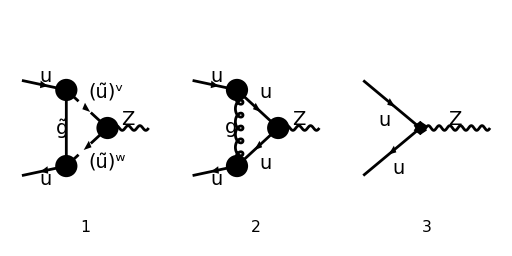

```mathematica
HTreeDiagrams = InsertFields[
	CreateTopologies[0, 2 -> 1],
	{F[3, {1}], -F[3, {1}]} -> {V[2]},
	InsertionLevel -> {Classes},
	Model -> MSSMQCD,
	Restrictions -> {NoLightFHCoupling, NoElectronHCoupling},
	ExcludeParticles -> {F[11|12],S[1|2|3|4],V[1|2|3]}
];
HLoopDiagrams = InsertFields[
	CreateTopologies[1, 2 -> 1, ExcludeTopologies->{Tadpoles, WFCorrections}], 
	{F[3, {1}], -F[3, {1}]} -> {V[2]},
	InsertionLevel -> {Classes},
	Model -> MSSMQCD,
	Restrictions -> {NoLightFHCoupling, NoElectronHCoupling},
	ExcludeParticles -> {F[11|12],S[1|2|3|4],V[1|2|3]}
];
HCTDiagrams = InsertFields[
	CreateCTTopologies[1, 2 -> 1, ExcludeTopologies->{TadpoleCTs, WFCorrectionCTs}], 
	{F[3, {1}], -F[3, {1}]} -> {V[2]},
	InsertionLevel -> {Classes},
	Model -> SMQCD,
	Restrictions -> {NoLightFHCoupling, NoElectronHCoupling},
	ExcludeParticles -> {F[11|12],S[1|2|3|4],V[1|3]}
];
Paint[HLoopDiagrams[[0]][Sequence@@HLoopDiagrams, Sequence@@HCTDiagrams], Numbering->Simple, ColumnsXRows -> {3, 1}, ImageSize->{512,256}];
```

Generating amplitudes from the diagrams. Note that the counterterm amplitude comes from the ordinary SMQCD, as its not implemented in MSSMQCD.
This leads to some patching, specifically using my own defined counterterms dQL, dQR, dZ.
The amplitudes are also generated without external polarization vectors.

```mathematica
MH0[0] = FCFAConvert[
	CreateFeynAmp[HTreeDiagrams], 
	IncomingMomenta -> {ki, kj},
	OutgoingMomenta -> {q},
	ChangeDimension -> D,
	UndoChiralSplittings -> True,
	List -> False,
	SMP -> True,
	DropSumOver -> True,
	LorentzIndexNames -> {μ, ν},
	FinalSubstitutions -> AmpSimplifyRules
] /.
Pair[LorentzIndex[μ,_],Momentum[Polarization[q,_],_]] -> 1;

MHLoop[0] = (FCFAConvert[
	CreateFeynAmp[HLoopDiagrams], 
	IncomingMomenta -> {ki, kj},
	OutgoingMomenta -> {q},
	LoopMomenta -> {qloop},
	ChangeDimension -> D,
	UndoChiralSplittings -> True,
	List -> False,
	SMP -> True,
	DropSumOver -> True,
	LorentzIndexNames -> {μ, ν},
	FinalSubstitutions -> AmpSimplifyRules
] /.
Pair[LorentzIndex[μ,_],Momentum[Polarization[q,_],_]] -> 1);

MHCT[0] = FCFAConvert[
	CreateFeynAmp[HCTDiagrams], 
	IncomingMomenta -> {ki, kj},
	OutgoingMomenta -> {q},
	ChangeDimension -> D,
	UndoChiralSplittings -> True,
	List -> False,
	SMP -> True,
	DropSumOver -> True,
	LorentzIndexNames -> {μ, ν},
	FinalSubstitutions -> AmpSimplifyRules
] /.
Pair[LorentzIndex[μ,_],Momentum[Polarization[q,_],_]] -> 1 /.
{dMf1[__]->0, dZfL1[__]->Re[dQL]+ⅈ Im[dQL],
	dZfR1[__]->Re[dQR]+ⅈ Im[dQR], SMP["m_u"]->0, dSW1->0, dZAZ1->0, dZZZ1->0, dZe1->0};
```

```mathematica
{MH0[1], MHLoop[1], MHCT[1]} = ReplaceAll[#, ZSimplifyRules] &/@ {MH0[0], MHLoop[0], MHCT[0]}
```

{-ⅈ (φ(-k_j)).(-ⅈ g_W γ^μ.(γ̄)^7 C_qqZ^L δ_Col1Col2-ⅈ g_W γ^μ.(γ̄)^6 C_qqZ^R δ_Col1Col2).(φ(k_i)),(g^Lor3ν (φ(-k_j)).(-ⅈ g_s γ^Lor3 T_Col2Col4^Glu4).(γ·(-qloop-k_j)).(-ⅈ g_W γ^μ.(γ̄)^7 C_qqZ^L-ⅈ g_W γ^μ.(γ̄)^6 C_qqZ^R).(γ·(q-qloop-k_j)).(-ⅈ γ^ν g_s T_Col4Col1^Glu4).(φ(k_i)))/(16 π^4 qloop^2.(k_j+qloop)^2.(k_j-q+qloop)^2)-(ⅈ g_W (q-2 qloop-2 k_j)^μ (-6 C_qqZ^L (cos(θ_W)) R_Sfe51^((ũ)_1) Conjugate[(R_Sfe41^((ũ)_1))]-6 C_qqZ^R (cos(θ_W)) R_Sfe52^((ũ)_1) Conjugate[(R_Sfe42^((ũ)_1))]) (φ(-k_j)).(ⅈ √2 (γ̄)^7 Conjugate[SqrtEGl] g_s T_Col2Col4^Glu4 Conjugate[(R_Sfe52^((ũ)_1))]-ⅈ √2 SqrtEGl (γ̄)^6 g_s T_Col2Col4^Glu4 Conjugate[(R_Sfe51^((ũ)_1))]).(m_(g̃)+γ·qloop).(ⅈ √2 SqrtEGl (γ̄)^6 g_s T_Col4Col1^Glu4 R_Sfe42^((ũ)_1)-ⅈ √2 (γ̄)^7 Conjugate[SqrtEGl] g_s T_Col4Col1^Glu4 R_Sfe41^((ũ)_1)).(φ(k_i)))/(96 π^4 (cos(θ_W)) (qloop^2-m_(g̃)^2).((k_j+qloop)^2-m_((ũ)_(1,Sfe5))^2).((k_j-q+qloop)^2-m_((ũ)_(1,Sfe4))^2)),-ⅈ (φ(-k_j)).((ⅈ g_W γ^μ.(γ̄)^7 δ_Col1Col2 (1/2 (Re(dQL)-ⅈ Im(dQL))+1/2 (Re(dQL)+ⅈ Im(dQL))) (C_qqZ^R (cos(θ_W))+1/2))/(cos(θ_W))+ⅈ g_W γ^μ.(γ̄)^6 C_qqZ^R δ_Col1Col2 (1/2 (Re(dQR)-ⅈ Im(dQR))+1/2 (Re(dQR)+ⅈ Im(dQR)))).(φ(k_i))}

For some reason, the simplification to Zqq-charges does not function properly for the counterterm.

```mathematica
MHCT[1] = -MHCT[1] /. Cq[R]SMP["cos_W"]+1/2->Cq[L]SMP["cos_W"]
```

ⅈ (φ(-k_j)).(ⅈ g_W γ^μ.(γ̄)^7 C_qqZ^L δ_Col1Col2 (1/2 (Re(dQL)-ⅈ Im(dQL))+1/2 (Re(dQL)+ⅈ Im(dQL)))+ⅈ g_W γ^μ.(γ̄)^6 C_qqZ^R δ_Col1Col2 (1/2 (Re(dQR)-ⅈ Im(dQR))+1/2 (Re(dQR)+ⅈ Im(dQR)))).(φ(k_i))

```mathematica
MHLoop[1] // SelectFree2[#, USf]& // DiracSimplify // SUNSimplify // Collect2[#, Cq, Factoring -> (Collect2[#, Spinor, Factoring -> Factor2]&)]&
MHLoop[1] // SelectNotFree2[#, USf]& // DiracSimplify // SUNSimplify // Factor2 // ReplaceAll[#, SqrtEGl SqrtEGl* -> 1]&
```

C_qqZ^R ((ⅈ C_F (φ(-k_j)).(γ·q).γ^μ.(γ·qloop).(γ̄)^6.(φ(k_i)) g_s^2 g_W δ_Col1Col2)/(8 π^4 qloop^2.(k_j+qloop)^2.(k_j-q+qloop)^2)-(ⅈ C_F (4-D) (φ(-k_j)).(γ·qloop).γ^μ.(γ·q).(γ̄)^6.(φ(k_i)) g_s^2 g_W δ_Col1Col2)/(16 π^4 qloop^2.(k_j+qloop)^2.(k_j-q+qloop)^2)+(ⅈ C_F (φ(-k_j)).(γ·q).(γ̄)^6.(φ(k_i)) k_j^μ g_s^2 g_W δ_Col1Col2)/(4 π^4 qloop^2.(k_j+qloop)^2.(k_j-q+qloop)^2)+(ⅈ C_F (2-D) (φ(-k_j)).(γ·qloop).(γ̄)^6.(φ(k_i)) (k_j^μ+qloop^μ) g_s^2 g_W δ_Col1Col2)/(8 π^4 qloop^2.(k_j+qloop)^2.(k_j-q+qloop)^2)-(ⅈ C_F (φ(-k_j)).γ^μ.(γ̄)^6.(φ(k_i)) (-D k_j^2+2 k_j^2+4 (k_j·q)-2 D (k_j·qloop)+4 (k_j·qloop)-D qloop^2+2 qloop^2) g_s^2 g_W δ_Col1Col2)/(16 π^4 qloop^2.(k_j+qloop)^2.(k_j-q+qloop)^2))+C_qqZ^L ((ⅈ C_F (φ(-k_j)).(γ·q).γ^μ.(γ·qloop).(γ̄)^7.(φ(k_i)) g_s^2 g_W δ_Col1Col2)/(8 π^4 qloop^2.(k_j+qloop)^2.(k_j-q+qloop)^2)-(ⅈ C_F (4-D) (φ(-k_j)).(γ·qloop).γ^μ.(γ·q).(γ̄)^7.(φ(k_i)) g_s^2 g_W δ_Col1Col2)/(16 π^4 qloop^2.(k_j+qloop)^2.(k_j-q+qloop)^2)+(ⅈ C_F (φ(-k_j)).(γ·q).(γ̄)^7.(φ(k_i)) k_j^μ g_s^2 g_W δ_Col1Col2)/(4 π^4 qloop^2.(k_j+qloop)^2.(k_j-q+qloop)^2)+(ⅈ C_F (2-D) (φ(-k_j)).(γ·qloop).(γ̄)^7.(φ(k_i)) (k_j^μ+qloop^μ) g_s^2 g_W δ_Col1Col2)/(8 π^4 qloop^2.(k_j+qloop)^2.(k_j-q+qloop)^2)-(ⅈ C_F (φ(-k_j)).γ^μ.(γ̄)^7.(φ(k_i)) (-D k_j^2+2 k_j^2+4 (k_j·q)-2 D (k_j·qloop)+4 (k_j·qloop)-D qloop^2+2 qloop^2) g_s^2 g_W δ_Col1Col2)/(16 π^4 qloop^2.(k_j+qloop)^2.(k_j-q+qloop)^2))

-((ⅈ C_F g_s^2 g_W δ_Col1Col2 (-q^μ+2 qloop^μ+2 k_j^μ) (C_qqZ^L R_Sfe51^((ũ)_1) Conjugate[(R_Sfe41^((ũ)_1))]+C_qqZ^R R_Sfe52^((ũ)_1) Conjugate[(R_Sfe42^((ũ)_1))]) (SqrtEGl^2 m_(g̃) R_Sfe42^((ũ)_1) Conjugate[(R_Sfe51^((ũ)_1))] (φ(-k_j)).(γ̄)^6.(φ(k_i))+(Conjugate[SqrtEGl])^2 m_(g̃) R_Sfe41^((ũ)_1) Conjugate[(R_Sfe52^((ũ)_1))] (φ(-k_j)).(γ̄)^7.(φ(k_i))-R_Sfe41^((ũ)_1) Conjugate[(R_Sfe51^((ũ)_1))] (φ(-k_j)).(γ·qloop).(γ̄)^7.(φ(k_i))-R_Sfe42^((ũ)_1) Conjugate[(R_Sfe52^((ũ)_1))] (φ(-k_j)).(γ·qloop).(γ̄)^6.(φ(k_i))))/(8 π^4 (qloop^2-m_(g̃)^2).((k_j+qloop)^2-m_((ũ)_(1,Sfe5))^2).((k_j-q+qloop)^2-m_((ũ)_(1,Sfe4))^2)))

```mathematica
MHLoop[1]/(CF SMP["g_W"] SMP["g_s"]^2/(16Pi^2) SDF[Col1,Col2]) // SelectFree2[#, USf]& // ReplaceAll[#, q -> ki+kj]& // DiracSimplify // SUNSimplify // TID[#, qloop, ToPaVe -> True, UsePaVeBasis -> True]& //
	ReplaceAll[#, Q2 -> s]& //
	PaVeReduce //
	DiracSimplify //
	FullSimplify
MHLoop[1]/(CF SMP["g_W"] SMP["g_s"]^2/(16Pi^2) SDF[Col1,Col2]) // SelectNotFree2[#, USf]& // ReplaceAll[#, q -> ki+kj]& // DiracSimplify // SUNSimplify // TID[#, qloop, ToPaVe -> True, UsePaVeBasis -> True]& //
	ReplaceAll[#, Q2 -> s]& //
	PaVeReduce //
	DiracSimplify //
	FullSimplify
```

1/(2 ((k_i·k_j)^2-k_i^2 k_j^2))(-2 D (k_i·k_j)^2 B_0(2 (k_i·k_j)+k_i^2+k_j^2,0,0)-4 B_0(k_i^2,0,0) (k_i·k_j)^2-4 B_0(k_j^2,0,0) (k_i·k_j)^2+14 (k_i·k_j)^2 B_0(2 (k_i·k_j)+k_i^2+k_j^2,0,0)-(2 (k_i·k_j)+k_i^2+k_j^2) (3 k_i^2 k_j^2-4 (k_i·k_j)^2) C_0(k_i^2,k_j^2,2 (k_i·k_j)+k_i^2+k_j^2,0,0,0)+2 D k_i^2 k_j^2 B_0(2 (k_i·k_j)+k_i^2+k_j^2,0,0)+3 k_i^2 k_j^2 B_0(k_i^2,0,0)+3 k_i^2 k_j^2 B_0(k_j^2,0,0)-k_i^2 (k_i·k_j) B_0(k_i^2,0,0)-k_j^2 (k_i·k_j) B_0(k_j^2,0,0)+k_i^2 (k_i·k_j) B_0(2 (k_i·k_j)+k_i^2+k_j^2,0,0)+k_j^2 (k_i·k_j) B_0(2 (k_i·k_j)+k_i^2+k_j^2,0,0)-12 k_i^2 k_j^2 B_0(2 (k_i·k_j)+k_i^2+k_j^2,0,0)) (C_qqZ^L (φ(-k_j)).γ^μ.(γ̄)^7.(φ(k_i))+C_qqZ^R (φ(-k_j)).γ^μ.(γ̄)^6.(φ(k_i)))

-1/((D-2) ((k_i·k_j)^2-k_i^2 k_j^2))(2 (D-2) m_(g̃) Conjugate[(R_Sfe51^((ũ)_1))] (φ(-k_j)).(γ̄)^6.(φ(k_i)) (k_j^μ k_i^2 B_0(k_i^2,m_(g̃)^2,m_((ũ)_(1,Sfe4))^2)-k_i^μ (k_i·k_j) B_0(k_i^2,m_(g̃)^2,m_((ũ)_(1,Sfe4))^2)+k_j^μ (k_i·k_j) B_0(k_j^2,m_(g̃)^2,m_((ũ)_(1,Sfe5))^2)-k_i^μ k_j^2 B_0(k_j^2,m_(g̃)^2,m_((ũ)_(1,Sfe5))^2)-k_j^μ k_i^2 B_0(k_i^2+2 (k_i·k_j)+k_j^2,m_((ũ)_(1,Sfe4))^2,m_((ũ)_(1,Sfe5))^2)+k_i^μ (k_i·k_j) B_0(k_i^2+2 (k_i·k_j)+k_j^2,m_((ũ)_(1,Sfe4))^2,m_((ũ)_(1,Sfe5))^2)-k_j^μ (k_i·k_j) B_0(k_i^2+2 (k_i·k_j)+k_j^2,m_((ũ)_(1,Sfe4))^2,m_((ũ)_(1,Sfe5))^2)+k_i^μ k_j^2 B_0(k_i^2+2 (k_i·k_j)+k_j^2,m_((ũ)_(1,Sfe4))^2,m_((ũ)_(1,Sfe5))^2)+(k_j^μ (-(k_i·k_j) (m_(g̃)^2-m_((ũ)_(1,Sfe4))^2+k_i·k_j)-k_i^2 (m_(g̃)^2-m_((ũ)_(1,Sfe5))^2+k_i·k_j))+k_i^μ ((k_i·k_j) (m_(g̃)^2-m_((ũ)_(1,Sfe5))^2+k_i·k_j)+(m_(g̃)^2-m_((ũ)_(1,Sfe4))^2+k_i·k_j) k_j^2)) C_0(k_i^2,k_j^2,k_i^2+2 (k_i·k_j)+k_j^2,m_((ũ)_(1,Sfe4))^2,m_(g̃)^2,m_((ũ)_(1,Sfe5))^2)) R_Sfe42^((ũ)_1) SqrtEGl^2+Conjugate[SqrtEGl] (k_j^2 C_0(k_i^2,k_j^2,k_i^2+2 (k_i·k_j)+k_j^2,m_((ũ)_(1,Sfe4))^2,m_(g̃)^2,m_((ũ)_(1,Sfe5))^2) k_i^4+(-((m_(g̃)^2-m_((ũ)_(1,Sfe5))^2+k_i·k_j+k_j^2) B_0(k_i^2,m_(g̃)^2,m_((ũ)_(1,Sfe4))^2))+(m_(g̃)^2-m_((ũ)_(1,Sfe5))^2+k_i·k_j) B_0(k_i^2+2 (k_i·k_j)+k_j^2,m_((ũ)_(1,Sfe4))^2,m_((ũ)_(1,Sfe5))^2)+(m_(g̃)^2-m_((ũ)_(1,Sfe5))^2) (m_(g̃)^2-m_((ũ)_(1,Sfe5))^2+2 (k_i·k_j)) C_0(k_i^2,k_j^2,k_i^2+2 (k_i·k_j)+k_j^2,m_((ũ)_(1,Sfe4))^2,m_(g̃)^2,m_((ũ)_(1,Sfe5))^2)+k_j^2 ((k_j^2-2 (m_((ũ)_(1,Sfe4))^2+m_((ũ)_(1,Sfe5))^2-k_i·k_j)) C_0(k_i^2,k_j^2,k_i^2+2 (k_i·k_j)+k_j^2,m_((ũ)_(1,Sfe4))^2,m_(g̃)^2,m_((ũ)_(1,Sfe5))^2)-B_0(k_j^2,m_(g̃)^2,m_((ũ)_(1,Sfe5))^2))) k_i^2+2 (k_i·k_j)^2 (2 C_0(k_i^2,k_j^2,k_i^2+2 (k_i·k_j)+k_j^2,m_((ũ)_(1,Sfe4))^2,m_(g̃)^2,m_((ũ)_(1,Sfe5))^2) m_(g̃)^2+B_0(k_i^2+2 (k_i·k_j)+k_j^2,m_((ũ)_(1,Sfe4))^2,m_((ũ)_(1,Sfe5))^2))+(m_(g̃)^2-m_((ũ)_(1,Sfe4))^2) k_j^2 (-B_0(k_j^2,m_(g̃)^2,m_((ũ)_(1,Sfe5))^2)+B_0(k_i^2+2 (k_i·k_j)+k_j^2,m_((ũ)_(1,Sfe4))^2,m_((ũ)_(1,Sfe5))^2)+(m_(g̃)^2-m_((ũ)_(1,Sfe4))^2) C_0(k_i^2,k_j^2,k_i^2+2 (k_i·k_j)+k_j^2,m_((ũ)_(1,Sfe4))^2,m_(g̃)^2,m_((ũ)_(1,Sfe5))^2))+(k_i·k_j) ((m_((ũ)_(1,Sfe4))^2-m_(g̃)^2) B_0(k_i^2,m_(g̃)^2,m_((ũ)_(1,Sfe4))^2)-(m_(g̃)^2-m_((ũ)_(1,Sfe5))^2+k_j^2) B_0(k_j^2,m_(g̃)^2,m_((ũ)_(1,Sfe5))^2)+(2 m_(g̃)^2-m_((ũ)_(1,Sfe4))^2-m_((ũ)_(1,Sfe5))^2+k_j^2) B_0(k_i^2+2 (k_i·k_j)+k_j^2,m_((ũ)_(1,Sfe4))^2,m_((ũ)_(1,Sfe5))^2)+2 (m_(g̃)^2-m_((ũ)_(1,Sfe4))^2) (m_(g̃)^2-m_((ũ)_(1,Sfe5))^2+k_j^2) C_0(k_i^2,k_j^2,k_i^2+2 (k_i·k_j)+k_j^2,m_((ũ)_(1,Sfe4))^2,m_(g̃)^2,m_((ũ)_(1,Sfe5))^2))) (Conjugate[(R_Sfe51^((ũ)_1))] (φ(-k_j)).γ^μ.(γ̄)^7.(φ(k_i)) R_Sfe41^((ũ)_1)+Conjugate[(R_Sfe52^((ũ)_1))] (φ(-k_j)).γ^μ.(γ̄)^6.(φ(k_i)) R_Sfe42^((ũ)_1)) SqrtEGl+2 (D-2) m_(g̃) (Conjugate[SqrtEGl])^2 Conjugate[(R_Sfe52^((ũ)_1))] (φ(-k_j)).(γ̄)^7.(φ(k_i)) (k_j^μ k_i^2 B_0(k_i^2,m_(g̃)^2,m_((ũ)_(1,Sfe4))^2)-k_i^μ (k_i·k_j) B_0(k_i^2,m_(g̃)^2,m_((ũ)_(1,Sfe4))^2)+k_j^μ (k_i·k_j) B_0(k_j^2,m_(g̃)^2,m_((ũ)_(1,Sfe5))^2)-k_i^μ k_j^2 B_0(k_j^2,m_(g̃)^2,m_((ũ)_(1,Sfe5))^2)-k_j^μ k_i^2 B_0(k_i^2+2 (k_i·k_j)+k_j^2,m_((ũ)_(1,Sfe4))^2,m_((ũ)_(1,Sfe5))^2)+k_i^μ (k_i·k_j) B_0(k_i^2+2 (k_i·k_j)+k_j^2,m_((ũ)_(1,Sfe4))^2,m_((ũ)_(1,Sfe5))^2)-k_j^μ (k_i·k_j) B_0(k_i^2+2 (k_i·k_j)+k_j^2,m_((ũ)_(1,Sfe4))^2,m_((ũ)_(1,Sfe5))^2)+k_i^μ k_j^2 B_0(k_i^2+2 (k_i·k_j)+k_j^2,m_((ũ)_(1,Sfe4))^2,m_((ũ)_(1,Sfe5))^2)+(k_j^μ (-(k_i·k_j) (m_(g̃)^2-m_((ũ)_(1,Sfe4))^2+k_i·k_j)-k_i^2 (m_(g̃)^2-m_((ũ)_(1,Sfe5))^2+k_i·k_j))+k_i^μ ((k_i·k_j) (m_(g̃)^2-m_((ũ)_(1,Sfe5))^2+k_i·k_j)+(m_(g̃)^2-m_((ũ)_(1,Sfe4))^2+k_i·k_j) k_j^2)) C_0(k_i^2,k_j^2,k_i^2+2 (k_i·k_j)+k_j^2,m_((ũ)_(1,Sfe4))^2,m_(g̃)^2,m_((ũ)_(1,Sfe5))^2)) R_Sfe41^((ũ)_1)) (Conjugate[(R_Sfe41^((ũ)_1))] C_qqZ^L R_Sfe51^((ũ)_1)+Conjugate[(R_Sfe42^((ũ)_1))] C_qqZ^R R_Sfe52^((ũ)_1))

## Set scalar products

Now, to set scalar products of the available momenta in preparation of evaluating the squared amplitudes.

```mathematica
SPD[ki, ki] = 0;
SPD[kj, kj] = 0;
SPD[q, q] = Q2;
SPD[ki, kj] = s/2;
SPD[ki, q] = s/2;
SPD[kj, q] = s/2;
SP[ki, ki] = 0;
SP[kj, kj] = 0;
SP[q, q] = Q2;
SP[ki, kj] = s/2;
SP[ki, q] = s/2;
SP[kj, q] = s/2;
```

For the loop-amplitude we can already insert the Passarino-Veltman functions.

```mathematica
MHLoop[2] = MHLoop[1] // TID[#, qloop, ToPaVe->True, UsePaVeBasis->True]&;
MHLoop[3] = MHLoop[2] // SUNSimplify;
```

## Evaluate square amplitudes

Here we square the individual factorised amplitudes.

### Hadron part

First import the quark counterterms and calculate the counterterm contribution to the hadronic tensor.

```mathematica
QuarkRenormalisation = Import[FileNameJoin[{ResultsDir, "quarkCTs.m"}]] /. {type -> 3, gen -> 1};
```

```mathematica
MHCT[2] = MHCT[1] // ReplaceAll[#, QuarkRenormalisation]&;
MHCT[2] // DiracSimplify // Simplify
```

-1/(4 π)C_F g_W α_s δ_Col1Col2 (C_qqZ^L (φ(-k_j)).γ^μ.(γ̄)^7.(φ(k_i)) (2 R_11^((ũ)_1) Conjugate[(R_11^((ũ)_1))] B_1(0,m_(g̃)^2,m_((ũ)_(1,1))^2)+2 R_21^((ũ)_1) Conjugate[(R_21^((ũ)_1))] B_1(0,m_(g̃)^2,m_((ũ)_(1,2))^2)+(ε-1) B_0(0,0,0))+C_qqZ^R (φ(-k_j)).γ^μ.(γ̄)^6.(φ(k_i)) (2 R_12^((ũ)_1) Conjugate[(R_12^((ũ)_1))] B_1(0,m_(g̃)^2,m_((ũ)_(1,1))^2)+2 R_22^((ũ)_1) Conjugate[(R_22^((ũ)_1))] B_1(0,m_(g̃)^2,m_((ũ)_(1,2))^2)+(ε-1) B_0(0,0,0)))

```mathematica
HadTensorCT[0] = (MH0[1]ConjugateAmplitude[MHCT[2]/.μ->ν] + (MHCT[2]/.μ->ν)ConjugateAmplitude[MH0[1]]) // FermionSpinSum // DiracSimplify;
HadTensorCT[1] = HadTensorCT[0] // SelectFree2[#, DiracTrace]& // Simplify;
```

Now to add the loop diagram contributions.

```mathematica
HadTensor[0] = ((MHLoop[3]/.μ->ν)ConjugateAmplitude[MH0[1]] + (MH0[1])ConjugateAmplitude[MHLoop[3]/.μ->ν]) // FermionSpinSum // DiracSimplify;
HadTensor[1] = SelectFree2[HadTensor[0], DiracTrace] + HadTensorCT[1];
```

A common prefactor can be extracted, and we can use that |SqrtEGl|.b2=1.

```mathematica
CommonPrefactor = CF^2/(32Pi^4)SMP["g_s"]^2SMP["g_W"]^2;
HadTensor[2] = CommonPrefactor(HadTensor[1]/CommonPrefactor // ReplaceAll[#, SqrtEGl*SqrtEGl->1]& //
	Collect2[#, Pair[__], Factoring->Simplify]&);
```

We can now explicitly do the sums over intermediary squarks, inserting the mixing angle under the assumptions of real squark mixing matrices.

```mathematica
temp = SelectFree2[HadTensor[2], Index[Sfermion,4|5]];
temp = temp + (SelectNotFree2[SelectFree2[HadTensor[2], Index[Sfermion,5]], Index[Sfermion[4]]] //
	Sum[#, {Index[Sfermion,4], 1, 2}]&);
temp = temp + (SelectNotFree2[SelectFree2[HadTensor[2], Index[Sfermion,4]], Index[Sfermion[5]]] //
	Sum[#, {Index[Sfermion,5], 1, 2}]&);
temp = temp + (SelectNotFree2[HadTensor[2], Index[Sfermion,4], Index[Sfermion,5]] //
	Sum[#, {Index[Sfermion,4], 1, 2}, {Index[Sfermion,5], 1, 2}]&);
HadTensor[3] = temp //
	ReplaceAll[#, Pair[idx_, Momentum[q,D]] -> Pair[idx, Momentum[ki,D]] + Pair[idx, Momentum[kj,D]]]& //
	Collect2[#, Pair[__], Factoring -> Simplify]&
Clear[temp];
```

-1/(16 π^2)C_F s g^μν g_W^2 (((4 Conjugate[C_00(0,Q2,Q2-s,m_(g̃)^2,m_((ũ)_(1,1))^2,m_((ũ)_(1,1))^2)] (Conjugate[(R_11^((ũ)_1))])^2 (R_11^((ũ)_1))^2+4 (Conjugate[(R_11^((ũ)_1))])^2 C_00(0,Q2,Q2-s,m_(g̃)^2,m_((ũ)_(1,1))^2,m_((ũ)_(1,1))^2) (R_11^((ũ)_1))^2+4 Conjugate[C_00(0,Q2,Q2-s,m_(g̃)^2,m_((ũ)_(1,1))^2,m_((ũ)_(1,2))^2)] Conjugate[(R_11^((ũ)_1))] Conjugate[(R_21^((ũ)_1))] R_21^((ũ)_1) R_11^((ũ)_1)+4 Conjugate[C_00(0,Q2,Q2-s,m_(g̃)^2,m_((ũ)_(1,2))^2,m_((ũ)_(1,1))^2)] Conjugate[(R_11^((ũ)_1))] Conjugate[(R_21^((ũ)_1))] R_21^((ũ)_1) R_11^((ũ)_1)+4 Conjugate[(R_11^((ũ)_1))] Conjugate[(R_21^((ũ)_1))] C_00(0,Q2,Q2-s,m_(g̃)^2,m_((ũ)_(1,1))^2,m_((ũ)_(1,2))^2) R_21^((ũ)_1) R_11^((ũ)_1)+4 Conjugate[(R_11^((ũ)_1))] Conjugate[(R_21^((ũ)_1))] C_00(0,Q2,Q2-s,m_(g̃)^2,m_((ũ)_(1,2))^2,m_((ũ)_(1,1))^2) R_21^((ũ)_1) R_11^((ũ)_1)+4 Conjugate[C_00(0,Q2,Q2-s,m_(g̃)^2,m_((ũ)_(1,2))^2,m_((ũ)_(1,2))^2)] (Conjugate[(R_21^((ũ)_1))])^2 (R_21^((ũ)_1))^2+4 (Conjugate[(R_21^((ũ)_1))])^2 C_00(0,Q2,Q2-s,m_(g̃)^2,m_((ũ)_(1,2))^2,m_((ũ)_(1,2))^2) (R_21^((ũ)_1))^2+(D-2) B_0(Q2-s,0,0)+(D-2) Conjugate[B_0(Q2-s,0,0)]+2 s Conjugate[C_1(0,Q2-s,Q2,0,0,0)]+D Q2 Conjugate[C_1(Q2,Q2-s,0,0,0,0)]-2 Q2 Conjugate[C_1(Q2,Q2-s,0,0,0,0)]-2 D Conjugate[C_00(0,Q2,Q2-s,0,0,0)]+4 Conjugate[C_00(0,Q2,Q2-s,0,0,0)]+2 s C_1(0,Q2-s,Q2,0,0,0)+D Q2 C_1(Q2,Q2-s,0,0,0,0)-2 Q2 C_1(Q2,Q2-s,0,0,0,0)-2 D C_00(0,Q2,Q2-s,0,0,0)+4 C_00(0,Q2,Q2-s,0,0,0)) g_s^2+4 π α_s (ε B_0(0,0,0)-B_0(0,0,0)+(ε-1) Conjugate[B_0(0,0,0)]+2 B_1(0,m_(g̃)^2,m_((ũ)_(1,1))^2) Conjugate[(R_11^((ũ)_1))] R_11^((ũ)_1)+2 Conjugate[B_1(0,m_(g̃)^2,m_((ũ)_(1,1))^2)] Conjugate[(R_11^((ũ)_1))] R_11^((ũ)_1)+2 B_1(0,m_(g̃)^2,m_((ũ)_(1,2))^2) Conjugate[(R_21^((ũ)_1))] R_21^((ũ)_1)+2 Conjugate[B_1(0,m_(g̃)^2,m_((ũ)_(1,2))^2)] Conjugate[(R_21^((ũ)_1))] R_21^((ũ)_1))) (C_qqZ^L)^2+4 C_qqZ^R g_s^2 (2 Conjugate[C_00(0,Q2,Q2-s,m_(g̃)^2,m_((ũ)_(1,1))^2,m_((ũ)_(1,1))^2)] Conjugate[(R_11^((ũ)_1))] Conjugate[(R_12^((ũ)_1))] R_11^((ũ)_1) R_12^((ũ)_1)+Conjugate[(R_11^((ũ)_1))] (2 Conjugate[(R_12^((ũ)_1))] C_00(0,Q2,Q2-s,m_(g̃)^2,m_((ũ)_(1,1))^2,m_((ũ)_(1,1))^2) R_11^((ũ)_1)+Conjugate[(R_22^((ũ)_1))] (Conjugate[C_00(0,Q2,Q2-s,m_(g̃)^2,m_((ũ)_(1,1))^2,m_((ũ)_(1,2))^2)]+Conjugate[C_00(0,Q2,Q2-s,m_(g̃)^2,m_((ũ)_(1,2))^2,m_((ũ)_(1,1))^2)]+C_00(0,Q2,Q2-s,m_(g̃)^2,m_((ũ)_(1,1))^2,m_((ũ)_(1,2))^2)+C_00(0,Q2,Q2-s,m_(g̃)^2,m_((ũ)_(1,2))^2,m_((ũ)_(1,1))^2)) R_21^((ũ)_1)) R_12^((ũ)_1)+Conjugate[(R_21^((ũ)_1))] (Conjugate[C_00(0,Q2,Q2-s,m_(g̃)^2,m_((ũ)_(1,1))^2,m_((ũ)_(1,2))^2)] Conjugate[(R_12^((ũ)_1))] R_11^((ũ)_1)+Conjugate[C_00(0,Q2,Q2-s,m_(g̃)^2,m_((ũ)_(1,2))^2,m_((ũ)_(1,1))^2)] Conjugate[(R_12^((ũ)_1))] R_11^((ũ)_1)+Conjugate[(R_12^((ũ)_1))] C_00(0,Q2,Q2-s,m_(g̃)^2,m_((ũ)_(1,1))^2,m_((ũ)_(1,2))^2) R_11^((ũ)_1)+Conjugate[(R_12^((ũ)_1))] C_00(0,Q2,Q2-s,m_(g̃)^2,m_((ũ)_(1,2))^2,m_((ũ)_(1,1))^2) R_11^((ũ)_1)+2 Conjugate[C_00(0,Q2,Q2-s,m_(g̃)^2,m_((ũ)_(1,2))^2,m_((ũ)_(1,2))^2)] Conjugate[(R_22^((ũ)_1))] R_21^((ũ)_1)+2 Conjugate[(R_22^((ũ)_1))] C_00(0,Q2,Q2-s,m_(g̃)^2,m_((ũ)_(1,2))^2,m_((ũ)_(1,2))^2) R_21^((ũ)_1)) R_22^((ũ)_1)) C_qqZ^L+(C_qqZ^R)^2 ((4 Conjugate[C_00(0,Q2,Q2-s,m_(g̃)^2,m_((ũ)_(1,1))^2,m_((ũ)_(1,1))^2)] (Conjugate[(R_12^((ũ)_1))])^2 (R_12^((ũ)_1))^2+4 (Conjugate[(R_12^((ũ)_1))])^2 C_00(0,Q2,Q2-s,m_(g̃)^2,m_((ũ)_(1,1))^2,m_((ũ)_(1,1))^2) (R_12^((ũ)_1))^2+4 Conjugate[C_00(0,Q2,Q2-s,m_(g̃)^2,m_((ũ)_(1,1))^2,m_((ũ)_(1,2))^2)] Conjugate[(R_12^((ũ)_1))] Conjugate[(R_22^((ũ)_1))] R_22^((ũ)_1) R_12^((ũ)_1)+4 Conjugate[C_00(0,Q2,Q2-s,m_(g̃)^2,m_((ũ)_(1,2))^2,m_((ũ)_(1,1))^2)] Conjugate[(R_12^((ũ)_1))] Conjugate[(R_22^((ũ)_1))] R_22^((ũ)_1) R_12^((ũ)_1)+4 Conjugate[(R_12^((ũ)_1))] Conjugate[(R_22^((ũ)_1))] C_00(0,Q2,Q2-s,m_(g̃)^2,m_((ũ)_(1,1))^2,m_((ũ)_(1,2))^2) R_22^((ũ)_1) R_12^((ũ)_1)+4 Conjugate[(R_12^((ũ)_1))] Conjugate[(R_22^((ũ)_1))] C_00(0,Q2,Q2-s,m_(g̃)^2,m_((ũ)_(1,2))^2,m_((ũ)_(1,1))^2) R_22^((ũ)_1) R_12^((ũ)_1)+4 Conjugate[C_00(0,Q2,Q2-s,m_(g̃)^2,m_((ũ)_(1,2))^2,m_((ũ)_(1,2))^2)] (Conjugate[(R_22^((ũ)_1))])^2 (R_22^((ũ)_1))^2+4 (Conjugate[(R_22^((ũ)_1))])^2 C_00(0,Q2,Q2-s,m_(g̃)^2,m_((ũ)_(1,2))^2,m_((ũ)_(1,2))^2) (R_22^((ũ)_1))^2+(D-2) B_0(Q2-s,0,0)+(D-2) Conjugate[B_0(Q2-s,0,0)]+2 s Conjugate[C_1(0,Q2-s,Q2,0,0,0)]+D Q2 Conjugate[C_1(Q2,Q2-s,0,0,0,0)]-2 Q2 Conjugate[C_1(Q2,Q2-s,0,0,0,0)]-2 D Conjugate[C_00(0,Q2,Q2-s,0,0,0)]+4 Conjugate[C_00(0,Q2,Q2-s,0,0,0)]+2 s C_1(0,Q2-s,Q2,0,0,0)+D Q2 C_1(Q2,Q2-s,0,0,0,0)-2 Q2 C_1(Q2,Q2-s,0,0,0,0)-2 D C_00(0,Q2,Q2-s,0,0,0)+4 C_00(0,Q2,Q2-s,0,0,0)) g_s^2+4 π α_s (ε B_0(0,0,0)-B_0(0,0,0)+(ε-1) Conjugate[B_0(0,0,0)]+2 B_1(0,m_(g̃)^2,m_((ũ)_(1,1))^2) Conjugate[(R_12^((ũ)_1))] R_12^((ũ)_1)+2 Conjugate[B_1(0,m_(g̃)^2,m_((ũ)_(1,1))^2)] Conjugate[(R_12^((ũ)_1))] R_12^((ũ)_1)+2 B_1(0,m_(g̃)^2,m_((ũ)_(1,2))^2) Conjugate[(R_22^((ũ)_1))] R_22^((ũ)_1)+2 Conjugate[B_1(0,m_(g̃)^2,m_((ũ)_(1,2))^2)] Conjugate[(R_22^((ũ)_1))] R_22^((ũ)_1)))) δ_Col1Col2^2+1/(8 π^2)C_F k_j^μ k_i^ν g_W^2 (((4 Conjugate[C_00(0,Q2,Q2-s,m_(g̃)^2,m_((ũ)_(1,1))^2,m_((ũ)_(1,1))^2)] (Conjugate[(R_11^((ũ)_1))])^2 (R_11^((ũ)_1))^2+4 (Conjugate[(R_11^((ũ)_1))])^2 C_00(0,Q2,Q2-s,m_(g̃)^2,m_((ũ)_(1,1))^2,m_((ũ)_(1,1))^2) (R_11^((ũ)_1))^2+4 Conjugate[C_00(0,Q2,Q2-s,m_(g̃)^2,m_((ũ)_(1,1))^2,m_((ũ)_(1,2))^2)] Conjugate[(R_11^((ũ)_1))] Conjugate[(R_21^((ũ)_1))] R_21^((ũ)_1) R_11^((ũ)_1)+4 Conjugate[C_00(0,Q2,Q2-s,m_(g̃)^2,m_((ũ)_(1,2))^2,m_((ũ)_(1,1))^2)] Conjugate[(R_11^((ũ)_1))] Conjugate[(R_21^((ũ)_1))] R_21^((ũ)_1) R_11^((ũ)_1)+4 Conjugate[(R_11^((ũ)_1))] Conjugate[(R_21^((ũ)_1))] C_00(0,Q2,Q2-s,m_(g̃)^2,m_((ũ)_(1,1))^2,m_((ũ)_(1,2))^2) R_21^((ũ)_1) R_11^((ũ)_1)+4 Conjugate[(R_11^((ũ)_1))] Conjugate[(R_21^((ũ)_1))] C_00(0,Q2,Q2-s,m_(g̃)^2,m_((ũ)_(1,2))^2,m_((ũ)_(1,1))^2) R_21^((ũ)_1) R_11^((ũ)_1)+4 Conjugate[C_00(0,Q2,Q2-s,m_(g̃)^2,m_((ũ)_(1,2))^2,m_((ũ)_(1,2))^2)] (Conjugate[(R_21^((ũ)_1))])^2 (R_21^((ũ)_1))^2+4 (Conjugate[(R_21^((ũ)_1))])^2 C_00(0,Q2,Q2-s,m_(g̃)^2,m_((ũ)_(1,2))^2,m_((ũ)_(1,2))^2) (R_21^((ũ)_1))^2+(D-2) B_0(Q2-s,0,0)+(D-2) Conjugate[B_0(Q2-s,0,0)]+2 s Conjugate[C_1(0,Q2-s,Q2,0,0,0)]+D Q2 Conjugate[C_1(Q2,Q2-s,0,0,0,0)]-2 Q2 Conjugate[C_1(Q2,Q2-s,0,0,0,0)]-2 D Conjugate[C_00(0,Q2,Q2-s,0,0,0)]+4 Conjugate[C_00(0,Q2,Q2-s,0,0,0)]+2 s C_1(0,Q2-s,Q2,0,0,0)+D Q2 C_1(Q2,Q2-s,0,0,0,0)-2 Q2 C_1(Q2,Q2-s,0,0,0,0)-2 D C_00(0,Q2,Q2-s,0,0,0)+4 C_00(0,Q2,Q2-s,0,0,0)) g_s^2+4 π α_s (ε B_0(0,0,0)-B_0(0,0,0)+(ε-1) Conjugate[B_0(0,0,0)]+2 B_1(0,m_(g̃)^2,m_((ũ)_(1,1))^2) Conjugate[(R_11^((ũ)_1))] R_11^((ũ)_1)+2 Conjugate[B_1(0,m_(g̃)^2,m_((ũ)_(1,1))^2)] Conjugate[(R_11^((ũ)_1))] R_11^((ũ)_1)+2 B_1(0,m_(g̃)^2,m_((ũ)_(1,2))^2) Conjugate[(R_21^((ũ)_1))] R_21^((ũ)_1)+2 Conjugate[B_1(0,m_(g̃)^2,m_((ũ)_(1,2))^2)] Conjugate[(R_21^((ũ)_1))] R_21^((ũ)_1))) (C_qqZ^L)^2+4 C_qqZ^R g_s^2 (2 Conjugate[C_00(0,Q2,Q2-s,m_(g̃)^2,m_((ũ)_(1,1))^2,m_((ũ)_(1,1))^2)] Conjugate[(R_11^((ũ)_1))] Conjugate[(R_12^((ũ)_1))] R_11^((ũ)_1) R_12^((ũ)_1)+Conjugate[(R_11^((ũ)_1))] (2 Conjugate[(R_12^((ũ)_1))] C_00(0,Q2,Q2-s,m_(g̃)^2,m_((ũ)_(1,1))^2,m_((ũ)_(1,1))^2) R_11^((ũ)_1)+Conjugate[(R_22^((ũ)_1))] (Conjugate[C_00(0,Q2,Q2-s,m_(g̃)^2,m_((ũ)_(1,1))^2,m_((ũ)_(1,2))^2)]+Conjugate[C_00(0,Q2,Q2-s,m_(g̃)^2,m_((ũ)_(1,2))^2,m_((ũ)_(1,1))^2)]+C_00(0,Q2,Q2-s,m_(g̃)^2,m_((ũ)_(1,1))^2,m_((ũ)_(1,2))^2)+C_00(0,Q2,Q2-s,m_(g̃)^2,m_((ũ)_(1,2))^2,m_((ũ)_(1,1))^2)) R_21^((ũ)_1)) R_12^((ũ)_1)+Conjugate[(R_21^((ũ)_1))] (Conjugate[C_00(0,Q2,Q2-s,m_(g̃)^2,m_((ũ)_(1,1))^2,m_((ũ)_(1,2))^2)] Conjugate[(R_12^((ũ)_1))] R_11^((ũ)_1)+Conjugate[C_00(0,Q2,Q2-s,m_(g̃)^2,m_((ũ)_(1,2))^2,m_((ũ)_(1,1))^2)] Conjugate[(R_12^((ũ)_1))] R_11^((ũ)_1)+Conjugate[(R_12^((ũ)_1))] C_00(0,Q2,Q2-s,m_(g̃)^2,m_((ũ)_(1,1))^2,m_((ũ)_(1,2))^2) R_11^((ũ)_1)+Conjugate[(R_12^((ũ)_1))] C_00(0,Q2,Q2-s,m_(g̃)^2,m_((ũ)_(1,2))^2,m_((ũ)_(1,1))^2) R_11^((ũ)_1)+2 Conjugate[C_00(0,Q2,Q2-s,m_(g̃)^2,m_((ũ)_(1,2))^2,m_((ũ)_(1,2))^2)] Conjugate[(R_22^((ũ)_1))] R_21^((ũ)_1)+2 Conjugate[(R_22^((ũ)_1))] C_00(0,Q2,Q2-s,m_(g̃)^2,m_((ũ)_(1,2))^2,m_((ũ)_(1,2))^2) R_21^((ũ)_1)) R_22^((ũ)_1)) C_qqZ^L+(C_qqZ^R)^2 ((4 Conjugate[C_00(0,Q2,Q2-s,m_(g̃)^2,m_((ũ)_(1,1))^2,m_((ũ)_(1,1))^2)] (Conjugate[(R_12^((ũ)_1))])^2 (R_12^((ũ)_1))^2+4 (Conjugate[(R_12^((ũ)_1))])^2 C_00(0,Q2,Q2-s,m_(g̃)^2,m_((ũ)_(1,1))^2,m_((ũ)_(1,1))^2) (R_12^((ũ)_1))^2+4 Conjugate[C_00(0,Q2,Q2-s,m_(g̃)^2,m_((ũ)_(1,1))^2,m_((ũ)_(1,2))^2)] Conjugate[(R_12^((ũ)_1))] Conjugate[(R_22^((ũ)_1))] R_22^((ũ)_1) R_12^((ũ)_1)+4 Conjugate[C_00(0,Q2,Q2-s,m_(g̃)^2,m_((ũ)_(1,2))^2,m_((ũ)_(1,1))^2)] Conjugate[(R_12^((ũ)_1))] Conjugate[(R_22^((ũ)_1))] R_22^((ũ)_1) R_12^((ũ)_1)+4 Conjugate[(R_12^((ũ)_1))] Conjugate[(R_22^((ũ)_1))] C_00(0,Q2,Q2-s,m_(g̃)^2,m_((ũ)_(1,1))^2,m_((ũ)_(1,2))^2) R_22^((ũ)_1) R_12^((ũ)_1)+4 Conjugate[(R_12^((ũ)_1))] Conjugate[(R_22^((ũ)_1))] C_00(0,Q2,Q2-s,m_(g̃)^2,m_((ũ)_(1,2))^2,m_((ũ)_(1,1))^2) R_22^((ũ)_1) R_12^((ũ)_1)+4 Conjugate[C_00(0,Q2,Q2-s,m_(g̃)^2,m_((ũ)_(1,2))^2,m_((ũ)_(1,2))^2)] (Conjugate[(R_22^((ũ)_1))])^2 (R_22^((ũ)_1))^2+4 (Conjugate[(R_22^((ũ)_1))])^2 C_00(0,Q2,Q2-s,m_(g̃)^2,m_((ũ)_(1,2))^2,m_((ũ)_(1,2))^2) (R_22^((ũ)_1))^2+(D-2) B_0(Q2-s,0,0)+(D-2) Conjugate[B_0(Q2-s,0,0)]+2 s Conjugate[C_1(0,Q2-s,Q2,0,0,0)]+D Q2 Conjugate[C_1(Q2,Q2-s,0,0,0,0)]-2 Q2 Conjugate[C_1(Q2,Q2-s,0,0,0,0)]-2 D Conjugate[C_00(0,Q2,Q2-s,0,0,0)]+4 Conjugate[C_00(0,Q2,Q2-s,0,0,0)]+2 s C_1(0,Q2-s,Q2,0,0,0)+D Q2 C_1(Q2,Q2-s,0,0,0,0)-2 Q2 C_1(Q2,Q2-s,0,0,0,0)-2 D C_00(0,Q2,Q2-s,0,0,0)+4 C_00(0,Q2,Q2-s,0,0,0)) g_s^2+4 π α_s (ε B_0(0,0,0)-B_0(0,0,0)+(ε-1) Conjugate[B_0(0,0,0)]+2 B_1(0,m_(g̃)^2,m_((ũ)_(1,1))^2) Conjugate[(R_12^((ũ)_1))] R_12^((ũ)_1)+2 Conjugate[B_1(0,m_(g̃)^2,m_((ũ)_(1,1))^2)] Conjugate[(R_12^((ũ)_1))] R_12^((ũ)_1)+2 B_1(0,m_(g̃)^2,m_((ũ)_(1,2))^2) Conjugate[(R_22^((ũ)_1))] R_22^((ũ)_1)+2 Conjugate[B_1(0,m_(g̃)^2,m_((ũ)_(1,2))^2)] Conjugate[(R_22^((ũ)_1))] R_22^((ũ)_1)))) δ_Col1Col2^2+1/(8 π^2)C_F k_i^μ k_j^ν g_W^2 (((4 Conjugate[C_00(0,Q2,Q2-s,m_(g̃)^2,m_((ũ)_(1,1))^2,m_((ũ)_(1,1))^2)] (Conjugate[(R_11^((ũ)_1))])^2 (R_11^((ũ)_1))^2+4 (Conjugate[(R_11^((ũ)_1))])^2 C_00(0,Q2,Q2-s,m_(g̃)^2,m_((ũ)_(1,1))^2,m_((ũ)_(1,1))^2) (R_11^((ũ)_1))^2+4 Conjugate[C_00(0,Q2,Q2-s,m_(g̃)^2,m_((ũ)_(1,1))^2,m_((ũ)_(1,2))^2)] Conjugate[(R_11^((ũ)_1))] Conjugate[(R_21^((ũ)_1))] R_21^((ũ)_1) R_11^((ũ)_1)+4 Conjugate[C_00(0,Q2,Q2-s,m_(g̃)^2,m_((ũ)_(1,2))^2,m_((ũ)_(1,1))^2)] Conjugate[(R_11^((ũ)_1))] Conjugate[(R_21^((ũ)_1))] R_21^((ũ)_1) R_11^((ũ)_1)+4 Conjugate[(R_11^((ũ)_1))] Conjugate[(R_21^((ũ)_1))] C_00(0,Q2,Q2-s,m_(g̃)^2,m_((ũ)_(1,1))^2,m_((ũ)_(1,2))^2) R_21^((ũ)_1) R_11^((ũ)_1)+4 Conjugate[(R_11^((ũ)_1))] Conjugate[(R_21^((ũ)_1))] C_00(0,Q2,Q2-s,m_(g̃)^2,m_((ũ)_(1,2))^2,m_((ũ)_(1,1))^2) R_21^((ũ)_1) R_11^((ũ)_1)+4 Conjugate[C_00(0,Q2,Q2-s,m_(g̃)^2,m_((ũ)_(1,2))^2,m_((ũ)_(1,2))^2)] (Conjugate[(R_21^((ũ)_1))])^2 (R_21^((ũ)_1))^2+4 (Conjugate[(R_21^((ũ)_1))])^2 C_00(0,Q2,Q2-s,m_(g̃)^2,m_((ũ)_(1,2))^2,m_((ũ)_(1,2))^2) (R_21^((ũ)_1))^2+(D-2) B_0(Q2-s,0,0)+(D-2) Conjugate[B_0(Q2-s,0,0)]+2 s Conjugate[C_1(0,Q2-s,Q2,0,0,0)]+D Q2 Conjugate[C_1(Q2,Q2-s,0,0,0,0)]-2 Q2 Conjugate[C_1(Q2,Q2-s,0,0,0,0)]-2 D Conjugate[C_00(0,Q2,Q2-s,0,0,0)]+4 Conjugate[C_00(0,Q2,Q2-s,0,0,0)]+2 s C_1(0,Q2-s,Q2,0,0,0)+D Q2 C_1(Q2,Q2-s,0,0,0,0)-2 Q2 C_1(Q2,Q2-s,0,0,0,0)-2 D C_00(0,Q2,Q2-s,0,0,0)+4 C_00(0,Q2,Q2-s,0,0,0)) g_s^2+4 π α_s (ε B_0(0,0,0)-B_0(0,0,0)+(ε-1) Conjugate[B_0(0,0,0)]+2 B_1(0,m_(g̃)^2,m_((ũ)_(1,1))^2) Conjugate[(R_11^((ũ)_1))] R_11^((ũ)_1)+2 Conjugate[B_1(0,m_(g̃)^2,m_((ũ)_(1,1))^2)] Conjugate[(R_11^((ũ)_1))] R_11^((ũ)_1)+2 B_1(0,m_(g̃)^2,m_((ũ)_(1,2))^2) Conjugate[(R_21^((ũ)_1))] R_21^((ũ)_1)+2 Conjugate[B_1(0,m_(g̃)^2,m_((ũ)_(1,2))^2)] Conjugate[(R_21^((ũ)_1))] R_21^((ũ)_1))) (C_qqZ^L)^2+4 C_qqZ^R g_s^2 (2 Conjugate[C_00(0,Q2,Q2-s,m_(g̃)^2,m_((ũ)_(1,1))^2,m_((ũ)_(1,1))^2)] Conjugate[(R_11^((ũ)_1))] Conjugate[(R_12^((ũ)_1))] R_11^((ũ)_1) R_12^((ũ)_1)+Conjugate[(R_11^((ũ)_1))] (2 Conjugate[(R_12^((ũ)_1))] C_00(0,Q2,Q2-s,m_(g̃)^2,m_((ũ)_(1,1))^2,m_((ũ)_(1,1))^2) R_11^((ũ)_1)+Conjugate[(R_22^((ũ)_1))] (Conjugate[C_00(0,Q2,Q2-s,m_(g̃)^2,m_((ũ)_(1,1))^2,m_((ũ)_(1,2))^2)]+Conjugate[C_00(0,Q2,Q2-s,m_(g̃)^2,m_((ũ)_(1,2))^2,m_((ũ)_(1,1))^2)]+C_00(0,Q2,Q2-s,m_(g̃)^2,m_((ũ)_(1,1))^2,m_((ũ)_(1,2))^2)+C_00(0,Q2,Q2-s,m_(g̃)^2,m_((ũ)_(1,2))^2,m_((ũ)_(1,1))^2)) R_21^((ũ)_1)) R_12^((ũ)_1)+Conjugate[(R_21^((ũ)_1))] (Conjugate[C_00(0,Q2,Q2-s,m_(g̃)^2,m_((ũ)_(1,1))^2,m_((ũ)_(1,2))^2)] Conjugate[(R_12^((ũ)_1))] R_11^((ũ)_1)+Conjugate[C_00(0,Q2,Q2-s,m_(g̃)^2,m_((ũ)_(1,2))^2,m_((ũ)_(1,1))^2)] Conjugate[(R_12^((ũ)_1))] R_11^((ũ)_1)+Conjugate[(R_12^((ũ)_1))] C_00(0,Q2,Q2-s,m_(g̃)^2,m_((ũ)_(1,1))^2,m_((ũ)_(1,2))^2) R_11^((ũ)_1)+Conjugate[(R_12^((ũ)_1))] C_00(0,Q2,Q2-s,m_(g̃)^2,m_((ũ)_(1,2))^2,m_((ũ)_(1,1))^2) R_11^((ũ)_1)+2 Conjugate[C_00(0,Q2,Q2-s,m_(g̃)^2,m_((ũ)_(1,2))^2,m_((ũ)_(1,2))^2)] Conjugate[(R_22^((ũ)_1))] R_21^((ũ)_1)+2 Conjugate[(R_22^((ũ)_1))] C_00(0,Q2,Q2-s,m_(g̃)^2,m_((ũ)_(1,2))^2,m_((ũ)_(1,2))^2) R_21^((ũ)_1)) R_22^((ũ)_1)) C_qqZ^L+(C_qqZ^R)^2 ((4 Conjugate[C_00(0,Q2,Q2-s,m_(g̃)^2,m_((ũ)_(1,1))^2,m_((ũ)_(1,1))^2)] (Conjugate[(R_12^((ũ)_1))])^2 (R_12^((ũ)_1))^2+4 (Conjugate[(R_12^((ũ)_1))])^2 C_00(0,Q2,Q2-s,m_(g̃)^2,m_((ũ)_(1,1))^2,m_((ũ)_(1,1))^2) (R_12^((ũ)_1))^2+4 Conjugate[C_00(0,Q2,Q2-s,m_(g̃)^2,m_((ũ)_(1,1))^2,m_((ũ)_(1,2))^2)] Conjugate[(R_12^((ũ)_1))] Conjugate[(R_22^((ũ)_1))] R_22^((ũ)_1) R_12^((ũ)_1)+4 Conjugate[C_00(0,Q2,Q2-s,m_(g̃)^2,m_((ũ)_(1,2))^2,m_((ũ)_(1,1))^2)] Conjugate[(R_12^((ũ)_1))] Conjugate[(R_22^((ũ)_1))] R_22^((ũ)_1) R_12^((ũ)_1)+4 Conjugate[(R_12^((ũ)_1))] Conjugate[(R_22^((ũ)_1))] C_00(0,Q2,Q2-s,m_(g̃)^2,m_((ũ)_(1,1))^2,m_((ũ)_(1,2))^2) R_22^((ũ)_1) R_12^((ũ)_1)+4 Conjugate[(R_12^((ũ)_1))] Conjugate[(R_22^((ũ)_1))] C_00(0,Q2,Q2-s,m_(g̃)^2,m_((ũ)_(1,2))^2,m_((ũ)_(1,1))^2) R_22^((ũ)_1) R_12^((ũ)_1)+4 Conjugate[C_00(0,Q2,Q2-s,m_(g̃)^2,m_((ũ)_(1,2))^2,m_((ũ)_(1,2))^2)] (Conjugate[(R_22^((ũ)_1))])^2 (R_22^((ũ)_1))^2+4 (Conjugate[(R_22^((ũ)_1))])^2 C_00(0,Q2,Q2-s,m_(g̃)^2,m_((ũ)_(1,2))^2,m_((ũ)_(1,2))^2) (R_22^((ũ)_1))^2+(D-2) B_0(Q2-s,0,0)+(D-2) Conjugate[B_0(Q2-s,0,0)]+2 s Conjugate[C_1(0,Q2-s,Q2,0,0,0)]+D Q2 Conjugate[C_1(Q2,Q2-s,0,0,0,0)]-2 Q2 Conjugate[C_1(Q2,Q2-s,0,0,0,0)]-2 D Conjugate[C_00(0,Q2,Q2-s,0,0,0)]+4 Conjugate[C_00(0,Q2,Q2-s,0,0,0)]+2 s C_1(0,Q2-s,Q2,0,0,0)+D Q2 C_1(Q2,Q2-s,0,0,0,0)-2 Q2 C_1(Q2,Q2-s,0,0,0,0)-2 D C_00(0,Q2,Q2-s,0,0,0)+4 C_00(0,Q2,Q2-s,0,0,0)) g_s^2+4 π α_s (ε B_0(0,0,0)-B_0(0,0,0)+(ε-1) Conjugate[B_0(0,0,0)]+2 B_1(0,m_(g̃)^2,m_((ũ)_(1,1))^2) Conjugate[(R_12^((ũ)_1))] R_12^((ũ)_1)+2 Conjugate[B_1(0,m_(g̃)^2,m_((ũ)_(1,1))^2)] Conjugate[(R_12^((ũ)_1))] R_12^((ũ)_1)+2 B_1(0,m_(g̃)^2,m_((ũ)_(1,2))^2) Conjugate[(R_22^((ũ)_1))] R_22^((ũ)_1)+2 Conjugate[B_1(0,m_(g̃)^2,m_((ũ)_(1,2))^2)] Conjugate[(R_22^((ũ)_1))] R_22^((ũ)_1)))) δ_Col1Col2^2

To get the final correct squared amplitude, we must contract the result with ϵ_μ(q)ϵ_ν*(q) to get the result and sum over the polarisations.

```mathematica
HadTensorContracted[0] = Pair[LorentzIndex[μ,D],Momentum[Polarization[q,-ⅈ],D]] Pair[LorentzIndex[ν,D],Momentum[Polarization[q,ⅈ],D]] HadTensor[3] // DoPolarizationSums[#, q]&;
HadTensorContracted[1] = HadTensorContracted[0] // Simplify // ReplaceAll[#, SqrtEGl*^p_ SqrtEGl^p_->1]& // FCReplaceD[#, D -> 4-2Epsilon]&

HadTensorCTContracted[0] = Pair[LorentzIndex[μ,D],Momentum[Polarization[q,-ⅈ],D]] Pair[LorentzIndex[ν,D],Momentum[Polarization[q,ⅈ],D]] HadTensorCT[1] // DoPolarizationSums[#, q]&;
HadTensorCTContracted[1] = HadTensorCTContracted[0] // Simplify // ReplaceAll[#, SqrtEGl*^p_ SqrtEGl^p_->1]&
```

1/(16 π^2 Q2)C_F s ((1-2 ε) Q2+s) g_W^2 δ_Col1Col2^2 (((4 Conjugate[C_00(0,Q2,Q2-s,m_(g̃)^2,m_((ũ)_(1,1))^2,m_((ũ)_(1,1))^2)] (Conjugate[(R_11^((ũ)_1))])^2 (R_11^((ũ)_1))^2+4 (Conjugate[(R_11^((ũ)_1))])^2 C_00(0,Q2,Q2-s,m_(g̃)^2,m_((ũ)_(1,1))^2,m_((ũ)_(1,1))^2) (R_11^((ũ)_1))^2+4 Conjugate[C_00(0,Q2,Q2-s,m_(g̃)^2,m_((ũ)_(1,1))^2,m_((ũ)_(1,2))^2)] Conjugate[(R_11^((ũ)_1))] Conjugate[(R_21^((ũ)_1))] R_21^((ũ)_1) R_11^((ũ)_1)+4 Conjugate[C_00(0,Q2,Q2-s,m_(g̃)^2,m_((ũ)_(1,2))^2,m_((ũ)_(1,1))^2)] Conjugate[(R_11^((ũ)_1))] Conjugate[(R_21^((ũ)_1))] R_21^((ũ)_1) R_11^((ũ)_1)+4 Conjugate[(R_11^((ũ)_1))] Conjugate[(R_21^((ũ)_1))] C_00(0,Q2,Q2-s,m_(g̃)^2,m_((ũ)_(1,1))^2,m_((ũ)_(1,2))^2) R_21^((ũ)_1) R_11^((ũ)_1)+4 Conjugate[(R_11^((ũ)_1))] Conjugate[(R_21^((ũ)_1))] C_00(0,Q2,Q2-s,m_(g̃)^2,m_((ũ)_(1,2))^2,m_((ũ)_(1,1))^2) R_21^((ũ)_1) R_11^((ũ)_1)+4 Conjugate[C_00(0,Q2,Q2-s,m_(g̃)^2,m_((ũ)_(1,2))^2,m_((ũ)_(1,2))^2)] (Conjugate[(R_21^((ũ)_1))])^2 (R_21^((ũ)_1))^2+4 (Conjugate[(R_21^((ũ)_1))])^2 C_00(0,Q2,Q2-s,m_(g̃)^2,m_((ũ)_(1,2))^2,m_((ũ)_(1,2))^2) (R_21^((ũ)_1))^2+(2-2 ε) B_0(Q2-s,0,0)+(2-2 ε) Conjugate[B_0(Q2-s,0,0)]+2 s Conjugate[C_1(0,Q2-s,Q2,0,0,0)]+(4-2 ε) Q2 Conjugate[C_1(Q2,Q2-s,0,0,0,0)]-2 Q2 Conjugate[C_1(Q2,Q2-s,0,0,0,0)]-2 (4-2 ε) Conjugate[C_00(0,Q2,Q2-s,0,0,0)]+4 Conjugate[C_00(0,Q2,Q2-s,0,0,0)]+2 s C_1(0,Q2-s,Q2,0,0,0)+(4-2 ε) Q2 C_1(Q2,Q2-s,0,0,0,0)-2 Q2 C_1(Q2,Q2-s,0,0,0,0)-2 (4-2 ε) C_00(0,Q2,Q2-s,0,0,0)+4 C_00(0,Q2,Q2-s,0,0,0)) g_s^2+4 π α_s (ε B_0(0,0,0)-B_0(0,0,0)+(ε-1) Conjugate[B_0(0,0,0)]+2 B_1(0,m_(g̃)^2,m_((ũ)_(1,1))^2) Conjugate[(R_11^((ũ)_1))] R_11^((ũ)_1)+2 Conjugate[B_1(0,m_(g̃)^2,m_((ũ)_(1,1))^2)] Conjugate[(R_11^((ũ)_1))] R_11^((ũ)_1)+2 B_1(0,m_(g̃)^2,m_((ũ)_(1,2))^2) Conjugate[(R_21^((ũ)_1))] R_21^((ũ)_1)+2 Conjugate[B_1(0,m_(g̃)^2,m_((ũ)_(1,2))^2)] Conjugate[(R_21^((ũ)_1))] R_21^((ũ)_1))) (C_qqZ^L)^2+4 C_qqZ^R g_s^2 (2 Conjugate[C_00(0,Q2,Q2-s,m_(g̃)^2,m_((ũ)_(1,1))^2,m_((ũ)_(1,1))^2)] Conjugate[(R_11^((ũ)_1))] Conjugate[(R_12^((ũ)_1))] R_11^((ũ)_1) R_12^((ũ)_1)+Conjugate[(R_11^((ũ)_1))] (2 Conjugate[(R_12^((ũ)_1))] C_00(0,Q2,Q2-s,m_(g̃)^2,m_((ũ)_(1,1))^2,m_((ũ)_(1,1))^2) R_11^((ũ)_1)+Conjugate[(R_22^((ũ)_1))] (Conjugate[C_00(0,Q2,Q2-s,m_(g̃)^2,m_((ũ)_(1,1))^2,m_((ũ)_(1,2))^2)]+Conjugate[C_00(0,Q2,Q2-s,m_(g̃)^2,m_((ũ)_(1,2))^2,m_((ũ)_(1,1))^2)]+C_00(0,Q2,Q2-s,m_(g̃)^2,m_((ũ)_(1,1))^2,m_((ũ)_(1,2))^2)+C_00(0,Q2,Q2-s,m_(g̃)^2,m_((ũ)_(1,2))^2,m_((ũ)_(1,1))^2)) R_21^((ũ)_1)) R_12^((ũ)_1)+Conjugate[(R_21^((ũ)_1))] (Conjugate[C_00(0,Q2,Q2-s,m_(g̃)^2,m_((ũ)_(1,1))^2,m_((ũ)_(1,2))^2)] Conjugate[(R_12^((ũ)_1))] R_11^((ũ)_1)+Conjugate[C_00(0,Q2,Q2-s,m_(g̃)^2,m_((ũ)_(1,2))^2,m_((ũ)_(1,1))^2)] Conjugate[(R_12^((ũ)_1))] R_11^((ũ)_1)+Conjugate[(R_12^((ũ)_1))] C_00(0,Q2,Q2-s,m_(g̃)^2,m_((ũ)_(1,1))^2,m_((ũ)_(1,2))^2) R_11^((ũ)_1)+Conjugate[(R_12^((ũ)_1))] C_00(0,Q2,Q2-s,m_(g̃)^2,m_((ũ)_(1,2))^2,m_((ũ)_(1,1))^2) R_11^((ũ)_1)+2 Conjugate[C_00(0,Q2,Q2-s,m_(g̃)^2,m_((ũ)_(1,2))^2,m_((ũ)_(1,2))^2)] Conjugate[(R_22^((ũ)_1))] R_21^((ũ)_1)+2 Conjugate[(R_22^((ũ)_1))] C_00(0,Q2,Q2-s,m_(g̃)^2,m_((ũ)_(1,2))^2,m_((ũ)_(1,2))^2) R_21^((ũ)_1)) R_22^((ũ)_1)) C_qqZ^L+(C_qqZ^R)^2 ((4 Conjugate[C_00(0,Q2,Q2-s,m_(g̃)^2,m_((ũ)_(1,1))^2,m_((ũ)_(1,1))^2)] (Conjugate[(R_12^((ũ)_1))])^2 (R_12^((ũ)_1))^2+4 (Conjugate[(R_12^((ũ)_1))])^2 C_00(0,Q2,Q2-s,m_(g̃)^2,m_((ũ)_(1,1))^2,m_((ũ)_(1,1))^2) (R_12^((ũ)_1))^2+4 Conjugate[C_00(0,Q2,Q2-s,m_(g̃)^2,m_((ũ)_(1,1))^2,m_((ũ)_(1,2))^2)] Conjugate[(R_12^((ũ)_1))] Conjugate[(R_22^((ũ)_1))] R_22^((ũ)_1) R_12^((ũ)_1)+4 Conjugate[C_00(0,Q2,Q2-s,m_(g̃)^2,m_((ũ)_(1,2))^2,m_((ũ)_(1,1))^2)] Conjugate[(R_12^((ũ)_1))] Conjugate[(R_22^((ũ)_1))] R_22^((ũ)_1) R_12^((ũ)_1)+4 Conjugate[(R_12^((ũ)_1))] Conjugate[(R_22^((ũ)_1))] C_00(0,Q2,Q2-s,m_(g̃)^2,m_((ũ)_(1,1))^2,m_((ũ)_(1,2))^2) R_22^((ũ)_1) R_12^((ũ)_1)+4 Conjugate[(R_12^((ũ)_1))] Conjugate[(R_22^((ũ)_1))] C_00(0,Q2,Q2-s,m_(g̃)^2,m_((ũ)_(1,2))^2,m_((ũ)_(1,1))^2) R_22^((ũ)_1) R_12^((ũ)_1)+4 Conjugate[C_00(0,Q2,Q2-s,m_(g̃)^2,m_((ũ)_(1,2))^2,m_((ũ)_(1,2))^2)] (Conjugate[(R_22^((ũ)_1))])^2 (R_22^((ũ)_1))^2+4 (Conjugate[(R_22^((ũ)_1))])^2 C_00(0,Q2,Q2-s,m_(g̃)^2,m_((ũ)_(1,2))^2,m_((ũ)_(1,2))^2) (R_22^((ũ)_1))^2+(2-2 ε) B_0(Q2-s,0,0)+(2-2 ε) Conjugate[B_0(Q2-s,0,0)]+2 s Conjugate[C_1(0,Q2-s,Q2,0,0,0)]+(4-2 ε) Q2 Conjugate[C_1(Q2,Q2-s,0,0,0,0)]-2 Q2 Conjugate[C_1(Q2,Q2-s,0,0,0,0)]-2 (4-2 ε) Conjugate[C_00(0,Q2,Q2-s,0,0,0)]+4 Conjugate[C_00(0,Q2,Q2-s,0,0,0)]+2 s C_1(0,Q2-s,Q2,0,0,0)+(4-2 ε) Q2 C_1(Q2,Q2-s,0,0,0,0)-2 Q2 C_1(Q2,Q2-s,0,0,0,0)-2 (4-2 ε) C_00(0,Q2,Q2-s,0,0,0)+4 C_00(0,Q2,Q2-s,0,0,0)) g_s^2+4 π α_s (ε B_0(0,0,0)-B_0(0,0,0)+(ε-1) Conjugate[B_0(0,0,0)]+2 B_1(0,m_(g̃)^2,m_((ũ)_(1,1))^2) Conjugate[(R_12^((ũ)_1))] R_12^((ũ)_1)+2 Conjugate[B_1(0,m_(g̃)^2,m_((ũ)_(1,1))^2)] Conjugate[(R_12^((ũ)_1))] R_12^((ũ)_1)+2 B_1(0,m_(g̃)^2,m_((ũ)_(1,2))^2) Conjugate[(R_22^((ũ)_1))] R_22^((ũ)_1)+2 Conjugate[B_1(0,m_(g̃)^2,m_((ũ)_(1,2))^2)] Conjugate[(R_22^((ũ)_1))] R_22^((ũ)_1))))

1/(4 π Q2)s C_F g_W^2 α_s δ_Col1Col2^2 ((D-3) Q2+s) ((C_qqZ^L)^2 (2 R_11^((ũ)_1) Conjugate[(R_11^((ũ)_1))] B_1(0,m_(g̃)^2,m_((ũ)_(1,1))^2)+2 R_11^((ũ)_1) Conjugate[(R_11^((ũ)_1))] Conjugate[B_1(0,m_(g̃)^2,m_((ũ)_(1,1))^2)]+2 R_21^((ũ)_1) Conjugate[(R_21^((ũ)_1))] B_1(0,m_(g̃)^2,m_((ũ)_(1,2))^2)+2 R_21^((ũ)_1) Conjugate[(R_21^((ũ)_1))] Conjugate[B_1(0,m_(g̃)^2,m_((ũ)_(1,2))^2)]+(ε-1) Conjugate[B_0(0,0,0)]+ε B_0(0,0,0)-B_0(0,0,0))+(C_qqZ^R)^2 (2 R_12^((ũ)_1) Conjugate[(R_12^((ũ)_1))] B_1(0,m_(g̃)^2,m_((ũ)_(1,1))^2)+2 R_12^((ũ)_1) Conjugate[(R_12^((ũ)_1))] Conjugate[B_1(0,m_(g̃)^2,m_((ũ)_(1,1))^2)]+2 R_22^((ũ)_1) Conjugate[(R_22^((ũ)_1))] B_1(0,m_(g̃)^2,m_((ũ)_(1,2))^2)+2 R_22^((ũ)_1) Conjugate[(R_22^((ũ)_1))] Conjugate[B_1(0,m_(g̃)^2,m_((ũ)_(1,2))^2)]+(ε-1) Conjugate[B_0(0,0,0)]+ε B_0(0,0,0)-B_0(0,0,0)))

```mathematica
HadTensorContracted[1] - HadTensorCTContracted[1] /. Epsilon -> (4-D)/2 /. Q2 -> s /. {SMP["g_s"]^2->4Pi SMP["alpha_s"], SMP["g_W"]^2 -> 4Pi alphaW} //
	SelectNotFree2[#, MSf]& // Collect2[#, {C0, PaVe}, Factoring -> FullSimplify]&
```

4 (D-2) s C_F α_s α_W δ_Col1Col2^2 (Abs[R_11^((ũ)_1)]^2 C_qqZ^L+Abs[R_12^((ũ)_1)]^2 C_qqZ^R)^2 Conjugate[C_00(0,0,s,m_((ũ)_(1,1))^2,m_(g̃)^2,m_((ũ)_(1,1))^2)]+4 (D-2) s C_F α_s α_W δ_Col1Col2^2 (Abs[R_21^((ũ)_1)]^2 C_qqZ^L+Abs[R_22^((ũ)_1)]^2 C_qqZ^R)^2 Conjugate[C_00(0,0,s,m_((ũ)_(1,2))^2,m_(g̃)^2,m_((ũ)_(1,2))^2)]+4 (D-2) s C_F α_s α_W δ_Col1Col2^2 (Abs[R_11^((ũ)_1)]^2 C_qqZ^L+Abs[R_12^((ũ)_1)]^2 C_qqZ^R)^2 C_00(0,0,s,m_((ũ)_(1,1))^2,m_(g̃)^2,m_((ũ)_(1,1))^2)+4 (D-2) s C_F α_s α_W δ_Col1Col2^2 (Abs[R_21^((ũ)_1)]^2 C_qqZ^L+Abs[R_22^((ũ)_1)]^2 C_qqZ^R)^2 C_00(0,0,s,m_((ũ)_(1,2))^2,m_(g̃)^2,m_((ũ)_(1,2))^2)+8 (D-2) s C_F α_s α_W δ_Col1Col2^2 (R_11^((ũ)_1) C_qqZ^L Conjugate[(R_21^((ũ)_1))]+R_12^((ũ)_1) C_qqZ^R Conjugate[(R_22^((ũ)_1))]) (R_21^((ũ)_1) C_qqZ^L Conjugate[(R_11^((ũ)_1))]+R_22^((ũ)_1) C_qqZ^R Conjugate[(R_12^((ũ)_1))]) Conjugate[C_00(0,0,s,m_((ũ)_(1,1))^2,m_(g̃)^2,m_((ũ)_(1,2))^2)]+8 (D-2) s C_F α_s α_W δ_Col1Col2^2 (R_11^((ũ)_1) C_qqZ^L Conjugate[(R_21^((ũ)_1))]+R_12^((ũ)_1) C_qqZ^R Conjugate[(R_22^((ũ)_1))]) (R_21^((ũ)_1) C_qqZ^L Conjugate[(R_11^((ũ)_1))]+R_22^((ũ)_1) C_qqZ^R Conjugate[(R_12^((ũ)_1))]) C_00(0,0,s,m_((ũ)_(1,1))^2,m_(g̃)^2,m_((ũ)_(1,2))^2)

## Phase Space Integration

Setting up some assumptions.

```mathematica
$Assumptions = {
	s ∈ PositiveReals,
	Q2 ∈ PositiveReals,
	MNeu[_] ∈ PositiveReals,
	z >= (MNeu[i]+MNeu[j])^2 / s,
	z <= 1,
	s >= (MNeu[i]+MNeu[j])^2,
	Q2 >= (MNeu[i]+MNeu[j])^2,
	p ∈ PositiveReals,
	Epsilon ∈ Reals,
	EpsilonUV ∈ NegativeReals,
	EpsilonIR ∈ PositiveReals,
	D ∈ PositiveReals,
	K1[_] ∈ Reals,
	K2[_] ∈ Reals,
	Subscript[θ, q] ∈ Reals,
	SMP[_] ∈ Reals,
	alphaW ∈ Reals,
	ScaleMu ∈ PositiveReals,
	EpsilonIR ∈ PositiveReals,
	EpsilonUV ∈ NegativeReals,
	EulerGamma ∈ PositiveReals,
	CF ∈ Reals,
	CA ∈ Reals,
	IdenticalPartFactor[__] ∈ Integers,
	CsqZ[1,1] ∈ Reals,
	CsqZ[2,2] ∈ Reals,
	Cq[_] ∈ Reals
};
```

### Neutralino tensor

Importing neutralino tensor.

```mathematica
NNTensor = Import[FileNameJoin[{LOResultsDir, "NNTensor.m"}]] //
	FeynAmpDenominatorExplicit //
	ReplaceAll[#, {Q2-DZ -> 1/Den[Q2,DZ], Q2-DZ* -> 1/Den[Q2,DZ*]}]&
```

(p ((2 g_W^2 (q̄)^μ (q̄)^ν 1/(Q2-Δ_Z) 1/(Q2-Conjugate[(Δ_Z)]) (m_i^2 (4 m_j^2+Q2)-2 m_i^4+Q2 m_j^2-2 m_j^4+Q2^2) (O_ij^(′′L) Conjugate[(O_ij^(′′L))]+O_ij^(′′R) Conjugate[(O_ij^(′′R))]))/(3 Q2^2)+(g_W^2 1/(Q2-Δ_Z) (ḡ)^μν 1/(Q2-Conjugate[(Δ_Z)]) (Conjugate[(O_ij^(′′L))] ((m_i^2 (Q2-2 m_j^2)+m_i^4+Q2 m_j^2+m_j^4-2 Q2^2) O_ij^(′′L)-6 Q2 m_i m_j O_ij^(′′R))+Conjugate[(O_ij^(′′R))] (-6 Q2 m_i m_j O_ij^(′′L)+(Q2 m_j^2+m_j^4-2 Q2^2) O_ij^(′′R)+m_i^2 (Q2-2 m_j^2) O_ij^(′′R)+m_i^4 O_ij^(′′R))))/(3 Q2)))/(4 π √Q2)

### Hadronic tensor

The phase space factor for a 2->1 process is simple.

```mathematica
PiHad = (2Pi)/s DiracDelta[1-z];
```

A common prefactor can to be extracted during calculation.

```mathematica
CommonPrefactor = 2Pi (D-2) CF SMP["alpha_s"]alphaW;
```

The scale factor μ is implicit in the Passarino-Veltman functions, so we need not add it here.

```mathematica
HadTensorResult = PiHad HadTensorContracted[1]/CommonPrefactor /. {SMP["g_s"]^2 -> 4Pi SMP["alpha_s"], SMP["g_W"]^2->4Pi alphaW} //
	ReplaceAll[#, Epsilon -> (4-D)/2]& //
	ReplaceAll[#, Q2 -> s]& //
	Collect2[#, DiracDelta[1-z], Factoring->Function[x, Collect2[x, {B0, B1, C0, PaVe}, Factoring -> FullSimplify]]]&
```

z-1 (4 Conjugate[C_00(0,0,s,m_((ũ)_(1,1))^2,m_(g̃)^2,m_((ũ)_(1,1))^2)] (C_qqZ^L Abs[R_11^((ũ)_1)]^2+Abs[R_12^((ũ)_1)]^2 C_qqZ^R)^2 δ_Col1Col2^2+4 Conjugate[C_00(0,0,s,m_((ũ)_(1,2))^2,m_(g̃)^2,m_((ũ)_(1,2))^2)] (C_qqZ^L Abs[R_21^((ũ)_1)]^2+Abs[R_22^((ũ)_1)]^2 C_qqZ^R)^2 δ_Col1Col2^2+1/2 (D-2) B_0(0,0,0) ((C_qqZ^L)^2+(C_qqZ^R)^2) δ_Col1Col2^2+1/2 (D-2) Conjugate[B_0(0,0,0)] ((C_qqZ^L)^2+(C_qqZ^R)^2) δ_Col1Col2^2+2 s Conjugate[C_1(0,0,s,0,0,0)] ((C_qqZ^L)^2+(C_qqZ^R)^2) δ_Col1Col2^2+(D-2) s Conjugate[C_1(0,s,0,0,0,0)] ((C_qqZ^L)^2+(C_qqZ^R)^2) δ_Col1Col2^2-2 (D-2) Conjugate[C_00(0,0,s,0,0,0)] ((C_qqZ^L)^2+(C_qqZ^R)^2) δ_Col1Col2^2+2 B_1(0,m_(g̃)^2,m_((ũ)_(1,1))^2) (Abs[R_11^((ũ)_1)]^2 (C_qqZ^L)^2+Abs[R_12^((ũ)_1)]^2 (C_qqZ^R)^2) δ_Col1Col2^2+2 Conjugate[B_1(0,m_(g̃)^2,m_((ũ)_(1,1))^2)] (Abs[R_11^((ũ)_1)]^2 (C_qqZ^L)^2+Abs[R_12^((ũ)_1)]^2 (C_qqZ^R)^2) δ_Col1Col2^2+2 B_1(0,m_(g̃)^2,m_((ũ)_(1,2))^2) (Abs[R_21^((ũ)_1)]^2 (C_qqZ^L)^2+Abs[R_22^((ũ)_1)]^2 (C_qqZ^R)^2) δ_Col1Col2^2+2 Conjugate[B_1(0,m_(g̃)^2,m_((ũ)_(1,2))^2)] (Abs[R_21^((ũ)_1)]^2 (C_qqZ^L)^2+Abs[R_22^((ũ)_1)]^2 (C_qqZ^R)^2) δ_Col1Col2^2+2 s ((C_qqZ^L)^2+(C_qqZ^R)^2) C_1(0,0,s,0,0,0) δ_Col1Col2^2+(D-2) s ((C_qqZ^L)^2+(C_qqZ^R)^2) C_1(0,s,0,0,0,0) δ_Col1Col2^2-2 (D-2) ((C_qqZ^L)^2+(C_qqZ^R)^2) C_00(0,0,s,0,0,0) δ_Col1Col2^2+4 (C_qqZ^L Abs[R_11^((ũ)_1)]^2+Abs[R_12^((ũ)_1)]^2 C_qqZ^R)^2 C_00(0,0,s,m_((ũ)_(1,1))^2,m_(g̃)^2,m_((ũ)_(1,1))^2) δ_Col1Col2^2+4 (C_qqZ^L Abs[R_21^((ũ)_1)]^2+Abs[R_22^((ũ)_1)]^2 C_qqZ^R)^2 C_00(0,0,s,m_((ũ)_(1,2))^2,m_(g̃)^2,m_((ũ)_(1,2))^2) δ_Col1Col2^2+8 Conjugate[C_00(0,0,s,m_((ũ)_(1,1))^2,m_(g̃)^2,m_((ũ)_(1,2))^2)] (Conjugate[(R_21^((ũ)_1))] C_qqZ^L R_11^((ũ)_1)+Conjugate[(R_22^((ũ)_1))] C_qqZ^R R_12^((ũ)_1)) (Conjugate[(R_11^((ũ)_1))] C_qqZ^L R_21^((ũ)_1)+Conjugate[(R_12^((ũ)_1))] C_qqZ^R R_22^((ũ)_1)) δ_Col1Col2^2+8 C_00(0,0,s,m_((ũ)_(1,1))^2,m_(g̃)^2,m_((ũ)_(1,2))^2) (Conjugate[(R_21^((ũ)_1))] C_qqZ^L R_11^((ũ)_1)+Conjugate[(R_22^((ũ)_1))] C_qqZ^R R_12^((ũ)_1)) (Conjugate[(R_11^((ũ)_1))] C_qqZ^L R_21^((ũ)_1)+Conjugate[(R_12^((ũ)_1))] C_qqZ^R R_22^((ũ)_1)) δ_Col1Col2^2)

```mathematica
HadTensorCTResult = PiHad HadTensorCTContracted[1]/CommonPrefactor /. {SMP["g_s"]^2 -> 4Pi SMP["alpha_s"], SMP["g_W"]^2->4Pi alphaW} //
	ReplaceAll[#, Epsilon -> (4-D)/2]& //
	ReplaceAll[#, Q2 -> s]& //
	Collect2[#, DiracDelta[1-z], Factoring->Function[x, Collect2[x, {B0, B1, C0, PaVe}, Factoring -> FullSimplify]]]&
```

z-1 (2 δ_Col1Col2^2 (Abs[R_11^((ũ)_1)]^2 (C_qqZ^L)^2+Abs[R_12^((ũ)_1)]^2 (C_qqZ^R)^2) Conjugate[B_1(0,m_(g̃)^2,m_((ũ)_(1,1))^2)]+2 δ_Col1Col2^2 (Abs[R_21^((ũ)_1)]^2 (C_qqZ^L)^2+Abs[R_22^((ũ)_1)]^2 (C_qqZ^R)^2) Conjugate[B_1(0,m_(g̃)^2,m_((ũ)_(1,2))^2)]+2 δ_Col1Col2^2 (Abs[R_11^((ũ)_1)]^2 (C_qqZ^L)^2+Abs[R_12^((ũ)_1)]^2 (C_qqZ^R)^2) B_1(0,m_(g̃)^2,m_((ũ)_(1,1))^2)+2 δ_Col1Col2^2 (Abs[R_21^((ũ)_1)]^2 (C_qqZ^L)^2+Abs[R_22^((ũ)_1)]^2 (C_qqZ^R)^2) B_1(0,m_(g̃)^2,m_((ũ)_(1,2))^2)-1/2 (D-2) δ_Col1Col2^2 Conjugate[B_0(0,0,0)] ((C_qqZ^L)^2+(C_qqZ^R)^2)-1/2 (D-2) B_0(0,0,0) δ_Col1Col2^2 ((C_qqZ^L)^2+(C_qqZ^R)^2))

```mathematica
HadTensorResult - HadTensorCTResult /. Epsilon -> (4-D)/2 /. Q2 -> s /. {SMP["g_s"]^2->4Pi SMP["alpha_s"], SMP["g_W"]^2 -> 4Pi alphaW} //
	SelectNotFree2[#, MSf]& // Collect2[#, {B0, B1, C0, PaVe}, Factoring -> FullSimplify]&
```

4 z-1 δ_Col1Col2^2 (Abs[R_11^((ũ)_1)]^2 C_qqZ^L+Abs[R_12^((ũ)_1)]^2 C_qqZ^R)^2 Conjugate[C_00(0,0,s,m_((ũ)_(1,1))^2,m_(g̃)^2,m_((ũ)_(1,1))^2)]+4 z-1 δ_Col1Col2^2 (Abs[R_21^((ũ)_1)]^2 C_qqZ^L+Abs[R_22^((ũ)_1)]^2 C_qqZ^R)^2 Conjugate[C_00(0,0,s,m_((ũ)_(1,2))^2,m_(g̃)^2,m_((ũ)_(1,2))^2)]+4 z-1 δ_Col1Col2^2 (Abs[R_11^((ũ)_1)]^2 C_qqZ^L+Abs[R_12^((ũ)_1)]^2 C_qqZ^R)^2 C_00(0,0,s,m_((ũ)_(1,1))^2,m_(g̃)^2,m_((ũ)_(1,1))^2)+4 z-1 δ_Col1Col2^2 (Abs[R_21^((ũ)_1)]^2 C_qqZ^L+Abs[R_22^((ũ)_1)]^2 C_qqZ^R)^2 C_00(0,0,s,m_((ũ)_(1,2))^2,m_(g̃)^2,m_((ũ)_(1,2))^2)+8 z-1 δ_Col1Col2^2 (R_11^((ũ)_1) C_qqZ^L Conjugate[(R_21^((ũ)_1))]+R_12^((ũ)_1) C_qqZ^R Conjugate[(R_22^((ũ)_1))]) (R_21^((ũ)_1) C_qqZ^L Conjugate[(R_11^((ũ)_1))]+R_22^((ũ)_1) C_qqZ^R Conjugate[(R_12^((ũ)_1))]) Conjugate[C_00(0,0,s,m_((ũ)_(1,1))^2,m_(g̃)^2,m_((ũ)_(1,2))^2)]+8 z-1 δ_Col1Col2^2 (R_11^((ũ)_1) C_qqZ^L Conjugate[(R_21^((ũ)_1))]+R_12^((ũ)_1) C_qqZ^R Conjugate[(R_22^((ũ)_1))]) (R_21^((ũ)_1) C_qqZ^L Conjugate[(R_11^((ũ)_1))]+R_22^((ũ)_1) C_qqZ^R Conjugate[(R_12^((ũ)_1))]) C_00(0,0,s,m_((ũ)_(1,1))^2,m_(g̃)^2,m_((ũ)_(1,2))^2)

## Total Cross-Section

Importing Born cross-section and substituting shorthands for kinetic bits.

```mathematica
MakeBoxes[K1, TraditionalForm] = SubscriptBox["K", 1];
MakeBoxes[K2, TraditionalForm] = SubscriptBox["K", 2];
KineticTermShorthands = {
	MEW[i]^4:> -12K1[s] - MEW[i]^2(s-2MEW[j]^2) - s MEW[j]^2 - MEW[j]^4 + 2s^2,
	MEW[i] MEW[j] :> K2[s]/s};
```

```mathematica
BornXSec[0] = DiracDelta[1-z]/s(D-2)/2 Import[FileNameJoin[{LOResultsDir, "NNxsec_hino.m"}]] (*/.
	{Abs[a_] -> Sqrt[a*a], Re[a_ b_] -> 1/2(a b + a*b*), Re[a_] -> 1/2(a + a*)}*) /. Q2 -> s //
	ReplaceAll[#, KineticTermShorthands]&
BornXSec[1] = BornXSec[0] // FCReplaceD[#, D -> 4-2Epsilon]&;
```

(π (D-2) p z-1 α_W^2 (1/2)^(i,j) (4 K_1(s) (Abs[Z_((χ̃)_i^0(χ̃)_j^0)^LR]^2+Abs[Z_((χ̃)_i^0(χ̃)_j^0)^RL]^2+Abs[Z_((χ̃)_i^0(χ̃)_j^0)^LL]^2+Abs[Z_((χ̃)_i^0(χ̃)_j^0)^RR]^2)+4 K_2(s) Re(Z_((χ̃)_i^0(χ̃)_j^0)^LL Conjugate[(Z_((χ̃)_i^0(χ̃)_j^0)^LR)]+Conjugate[(Z_((χ̃)_i^0(χ̃)_j^0)^RR)] Z_((χ̃)_i^0(χ̃)_j^0)^RL)))/(2 s^(5/2) C_A)

### Calculate Total Cross-Section

Setting up the factor to multiply with the squared amplitudes.

```mathematica
XSecPrefactor = 1/(4Pi s)1/(4 CA^2)IdenticalPartFactor[i,j];
```

Computing the full renormalized vertex cross-section in  dimensions.

```mathematica
TotXSec[0] = XSecPrefactor CommonPrefactor ((-Coefficient[NNTensor, Pair[LorentzIndex[μ],LorentzIndex[ν]]]) HadTensorResult //
	ReplaceAll[#, SUNFDelta[a_, b_]^p_ -> CA]& //
	Expand //
	ReplaceAll[#, {SMP["g_W"] -> Sqrt[4Pi alphaW], SMP["g_s"] -> ScaleMu^((4-D)/2) Sqrt[4Pi SMP["alpha_s"]]}]& //
	ReplaceAll[#, {USf[3,1] -> USf[5,g], MSf[A_,3,1] -> MSf[A,5,g]}]& //
	ReplaceRepeated[#, SuperChargeRules]& //
	ReplaceAll[#, Q2 -> s]& //
	ReplaceAll[#, KineticTermShorthands]& //
	ReplaceAll[#, (h:B0|B1|C0|PaVe)[args__] -> Re[h[args]] + ⅈ Im[h[args]]]& //
	Collect2[#, DiracDelta[1-z], Factoring -> (Collect2[#, {K1[s], K2[s]}, Factoring -> CollectEffCharges]&)]& //
	ReplaceRepeated[#, {a_*b_ + a_**b_* -> 2 Re[a*b], a_*b_* + a_**b_ -> 2Re[a*b*], a_*a_* -> Abs[a]^2}]& //
	FRH)
```

1/(8 C_A^2 s)α_W C_F (D-2) z-1 (1/2)^(i,j) α_s (K_2(s) (1/s^(3/2)4 α_W C_A p Re(Conjugate[(Z_((χ̃)_i^0(χ̃)_j^0)^LR)] Z_((χ̃)_i^0(χ̃)_j^0)^LL) ((D-2) Re(B_0(0,0,0))+2 (4 Re(C_00(0,0,s,m_((q̃)_(g,1))^2,m_(g̃)^2,m_((q̃)_(g,1))^2)) Abs[R_11^((q̃)_g)]^4+2 Re(B_1(0,m_(g̃)^2,m_((q̃)_(g,1))^2)) Abs[R_11^((q̃)_g)]^2+2 Abs[R_21^((q̃)_g)]^2 Re(B_1(0,m_(g̃)^2,m_((q̃)_(g,2))^2))+2 s Re(C_1(0,0,s,0,0,0))+D s Re(C_1(0,s,0,0,0,0))-2 s Re(C_1(0,s,0,0,0,0))-2 D Re(C_00(0,0,s,0,0,0))+4 Re(C_00(0,0,s,0,0,0))+4 Abs[R_21^((q̃)_g)]^4 Re(C_00(0,0,s,m_((q̃)_(g,2))^2,m_(g̃)^2,m_((q̃)_(g,2))^2))+8 Conjugate[(R_11^((q̃)_g))] Conjugate[(R_21^((q̃)_g))] Re(C_00(0,0,s,m_((q̃)_(g,1))^2,m_(g̃)^2,m_((q̃)_(g,2))^2)) R_11^((q̃)_g) R_21^((q̃)_g)))+1/s^(3/2)4 α_W C_A p Re(Conjugate[(Z_((χ̃)_i^0(χ̃)_j^0)^RR)] Z_((χ̃)_i^0(χ̃)_j^0)^RL) ((D-2) Re(B_0(0,0,0))+2 (4 Re(C_00(0,0,s,m_((q̃)_(g,1))^2,m_(g̃)^2,m_((q̃)_(g,1))^2)) Abs[R_12^((q̃)_g)]^4+2 Re(B_1(0,m_(g̃)^2,m_((q̃)_(g,1))^2)) Abs[R_12^((q̃)_g)]^2+2 Abs[R_22^((q̃)_g)]^2 Re(B_1(0,m_(g̃)^2,m_((q̃)_(g,2))^2))+2 s Re(C_1(0,0,s,0,0,0))+D s Re(C_1(0,s,0,0,0,0))-2 s Re(C_1(0,s,0,0,0,0))-2 D Re(C_00(0,0,s,0,0,0))+4 Re(C_00(0,0,s,0,0,0))+4 Abs[R_22^((q̃)_g)]^4 Re(C_00(0,0,s,m_((q̃)_(g,2))^2,m_(g̃)^2,m_((q̃)_(g,2))^2))+8 Conjugate[(R_12^((q̃)_g))] Conjugate[(R_22^((q̃)_g))] Re(C_00(0,0,s,m_((q̃)_(g,1))^2,m_(g̃)^2,m_((q̃)_(g,2))^2)) R_12^((q̃)_g) R_22^((q̃)_g)))+1/s^(3/2)32 α_W C_A p (Abs[R_11^((q̃)_g)]^2 Re(C_00(0,0,s,m_((q̃)_(g,1))^2,m_(g̃)^2,m_((q̃)_(g,1))^2)) Abs[R_12^((q̃)_g)]^2+Abs[R_21^((q̃)_g)]^2 Abs[R_22^((q̃)_g)]^2 Re(C_00(0,0,s,m_((q̃)_(g,2))^2,m_(g̃)^2,m_((q̃)_(g,2))^2))+Re(C_00(0,0,s,m_((q̃)_(g,1))^2,m_(g̃)^2,m_((q̃)_(g,2))^2)) (Conjugate[(R_11^((q̃)_g))] Conjugate[(R_22^((q̃)_g))] R_12^((q̃)_g) R_21^((q̃)_g)+Conjugate[(R_12^((q̃)_g))] Conjugate[(R_21^((q̃)_g))] R_11^((q̃)_g) R_22^((q̃)_g))) (Conjugate[(Z_((χ̃)_i^0(χ̃)_j^0)^RR)] Z_((χ̃)_i^0(χ̃)_j^0)^LL+Conjugate[(Z_((χ̃)_i^0(χ̃)_j^0)^RL)] Z_((χ̃)_i^0(χ̃)_j^0)^LR))+K_1(s) (1/s^(3/2)4 α_W C_A p (Abs[Z_((χ̃)_i^0(χ̃)_j^0)^LL]^2+Abs[Z_((χ̃)_i^0(χ̃)_j^0)^LR]^2) ((D-2) Re(B_0(0,0,0))+2 (4 Re(C_00(0,0,s,m_((q̃)_(g,1))^2,m_(g̃)^2,m_((q̃)_(g,1))^2)) Abs[R_11^((q̃)_g)]^4+2 Re(B_1(0,m_(g̃)^2,m_((q̃)_(g,1))^2)) Abs[R_11^((q̃)_g)]^2+2 Abs[R_21^((q̃)_g)]^2 Re(B_1(0,m_(g̃)^2,m_((q̃)_(g,2))^2))+2 s Re(C_1(0,0,s,0,0,0))+D s Re(C_1(0,s,0,0,0,0))-2 s Re(C_1(0,s,0,0,0,0))-2 D Re(C_00(0,0,s,0,0,0))+4 Re(C_00(0,0,s,0,0,0))+4 Abs[R_21^((q̃)_g)]^4 Re(C_00(0,0,s,m_((q̃)_(g,2))^2,m_(g̃)^2,m_((q̃)_(g,2))^2))+8 Conjugate[(R_11^((q̃)_g))] Conjugate[(R_21^((q̃)_g))] Re(C_00(0,0,s,m_((q̃)_(g,1))^2,m_(g̃)^2,m_((q̃)_(g,2))^2)) R_11^((q̃)_g) R_21^((q̃)_g)))+1/s^(3/2)4 α_W C_A p (Abs[Z_((χ̃)_i^0(χ̃)_j^0)^RL]^2+Abs[Z_((χ̃)_i^0(χ̃)_j^0)^RR]^2) ((D-2) Re(B_0(0,0,0))+2 (4 Re(C_00(0,0,s,m_((q̃)_(g,1))^2,m_(g̃)^2,m_((q̃)_(g,1))^2)) Abs[R_12^((q̃)_g)]^4+2 Re(B_1(0,m_(g̃)^2,m_((q̃)_(g,1))^2)) Abs[R_12^((q̃)_g)]^2+2 Abs[R_22^((q̃)_g)]^2 Re(B_1(0,m_(g̃)^2,m_((q̃)_(g,2))^2))+2 s Re(C_1(0,0,s,0,0,0))+D s Re(C_1(0,s,0,0,0,0))-2 s Re(C_1(0,s,0,0,0,0))-2 D Re(C_00(0,0,s,0,0,0))+4 Re(C_00(0,0,s,0,0,0))+4 Abs[R_22^((q̃)_g)]^4 Re(C_00(0,0,s,m_((q̃)_(g,2))^2,m_(g̃)^2,m_((q̃)_(g,2))^2))+8 Conjugate[(R_12^((q̃)_g))] Conjugate[(R_22^((q̃)_g))] Re(C_00(0,0,s,m_((q̃)_(g,1))^2,m_(g̃)^2,m_((q̃)_(g,2))^2)) R_12^((q̃)_g) R_22^((q̃)_g)))+1/s^(3/2)64 α_W C_A p (Abs[R_11^((q̃)_g)]^2 Re(C_00(0,0,s,m_((q̃)_(g,1))^2,m_(g̃)^2,m_((q̃)_(g,1))^2)) Abs[R_12^((q̃)_g)]^2+Abs[R_21^((q̃)_g)]^2 Abs[R_22^((q̃)_g)]^2 Re(C_00(0,0,s,m_((q̃)_(g,2))^2,m_(g̃)^2,m_((q̃)_(g,2))^2))+Re(C_00(0,0,s,m_((q̃)_(g,1))^2,m_(g̃)^2,m_((q̃)_(g,2))^2)) (Conjugate[(R_11^((q̃)_g))] Conjugate[(R_22^((q̃)_g))] R_12^((q̃)_g) R_21^((q̃)_g)+Conjugate[(R_12^((q̃)_g))] Conjugate[(R_21^((q̃)_g))] R_11^((q̃)_g) R_22^((q̃)_g))) (Conjugate[(Z_((χ̃)_i^0(χ̃)_j^0)^RL)] Z_((χ̃)_i^0(χ̃)_j^0)^LL+Conjugate[(Z_((χ̃)_i^0(χ̃)_j^0)^RR)] Z_((χ̃)_i^0(χ̃)_j^0)^LR)))

```mathematica
TotXSec[1] = TotXSec[0] /. (h:PaVe|B0|B1)[args__] -> PaVeTore2FC h[args] // Refine;
```

```mathematica
TotXSecCT[0] = XSecPrefactor CommonPrefactor ((-Coefficient[NNTensor, Pair[LorentzIndex[μ],LorentzIndex[ν]]]) HadTensorCTResult //
	ReplaceAll[#, SUNFDelta[a_, b_]^p_ -> CA]& //
	Expand //
	ReplaceAll[#, {SMP["g_W"] -> Sqrt[4Pi alphaW], SMP["g_s"]-> ScaleMu^((4-D)/2) Sqrt[4Pi SMP["alpha_s"]]}]& //
	ReplaceAll[#, {USf[3,1] -> USf[5,g], MSf[A_,3,1] -> MSf[A,5,g]}]& //
	ReplaceRepeated[#, SuperChargeRules]& //
	ReplaceAll[#, Q2->s]& //
	ReplaceAll[#, KineticTermShorthands]& //
	ReplaceAll[#, (h:B0|B1|C0|PaVe)[args__] -> Re[h[args]] + ⅈ Im[h[args]]]& //
	Collect2[#, DiracDelta[1-z], Factoring->CollectEffCharges]& //
	ReplaceRepeated[#, {a_*b_ + a_**b_* -> 2 Re[a*b], a_*b_* + a_**b_ -> 2Re[a*b*], a_*a_* -> Abs[a]^2}]& //
	FRH)
```

1/(8 s C_A^2)(D-2) C_F z-1 α_s α_W (1/2)^(i,j) (-(4 p C_A K_2(s) α_W Re(Z_((χ̃)_i^0(χ̃)_j^0)^LL Conjugate[(Z_((χ̃)_i^0(χ̃)_j^0)^LR)]) ((D-2) Re(B_0(0,0,0))-4 (Abs[R_11^((q̃)_g)]^2 Re(B_1(0,m_(g̃)^2,m_((q̃)_(g,1))^2))+Abs[R_21^((q̃)_g)]^2 Re(B_1(0,m_(g̃)^2,m_((q̃)_(g,2))^2)))))/s^(3/2)-(4 p C_A K_2(s) α_W Re(Conjugate[(Z_((χ̃)_i^0(χ̃)_j^0)^RR)] Z_((χ̃)_i^0(χ̃)_j^0)^RL) ((D-2) Re(B_0(0,0,0))-4 (Abs[R_12^((q̃)_g)]^2 Re(B_1(0,m_(g̃)^2,m_((q̃)_(g,1))^2))+Abs[R_22^((q̃)_g)]^2 Re(B_1(0,m_(g̃)^2,m_((q̃)_(g,2))^2)))))/s^(3/2)-(4 p C_A K_1(s) α_W (Abs[Z_((χ̃)_i^0(χ̃)_j^0)^LR]^2+Abs[Z_((χ̃)_i^0(χ̃)_j^0)^LL]^2) ((D-2) Re(B_0(0,0,0))-4 (Abs[R_11^((q̃)_g)]^2 Re(B_1(0,m_(g̃)^2,m_((q̃)_(g,1))^2))+Abs[R_21^((q̃)_g)]^2 Re(B_1(0,m_(g̃)^2,m_((q̃)_(g,2))^2)))))/s^(3/2)-(4 p C_A K_1(s) α_W (Abs[Z_((χ̃)_i^0(χ̃)_j^0)^RL]^2+Abs[Z_((χ̃)_i^0(χ̃)_j^0)^RR]^2) ((D-2) Re(B_0(0,0,0))-4 (Abs[R_12^((q̃)_g)]^2 Re(B_1(0,m_(g̃)^2,m_((q̃)_(g,1))^2))+Abs[R_22^((q̃)_g)]^2 Re(B_1(0,m_(g̃)^2,m_((q̃)_(g,2))^2)))))/s^(3/2))

```mathematica
TotXSecCT[1] = TotXSecCT[0] /. (h:PaVe|B0|B1)[args__] -> PaVeTore2FC h[args] // Refine;
```

### Comparison with Tore

```mathematica
rGamma = (Gamma[1-Epsilon]^2Gamma[1+Epsilon])/Gamma[1-2Epsilon] /. Epsilon -> (4-D)/2 // Simplify;
TorePaVePrefactor = ((4Pi)^(D/2)ScaleMu^(4-D))/(ⅈ rGamma)1/(2Pi)^D;
FCPaVePrefactor = (2Pi ScaleMu)^(4-D)/(ⅈ Pi^2)(*(2Pi)^(D-4)*);
PXPaVePrefactor = (4Pi)^(D/2)/(ⅈ Exp[-EulerGamma * ((4-D)/2)])ScaleMu^(4-D)1/(2Pi)^D;
PaVeTore2FC = FCPaVePrefactor/TorePaVePrefactor
PaVeTore2PX = PXPaVePrefactor/TorePaVePrefactor
PaVeFC2PX = PXPaVePrefactor/FCPaVePrefactor
```

(2^(4-D) π^(2-D/2) 3-D/2 (D/2-1)^2)/(D-3)

(ⅇ^(1/2 ℽ (4-D)) 3-D/2 (D/2-1)^2)/(D-3)

2^(D-4) ⅇ^(1/2 ℽ (4-D)) π^(D/2-2)

```mathematica
paveArgs = {{0,s,0},{0,0,0}};
TorePaVe[idx_] := PaVe[idx, Sequence@@paveArgs]
TorePaVe[idx1_, idx2_] := PaVe[idx1, idx2, Sequence@@paveArgs]
paveFactor = (D-2)^2 TorePaVe[0,0] - s((D-2)TorePaVe[1,2] + 2(TorePaVe[0]+TorePaVe[1]+TorePaVe[2]));
LoopResultTore = 2CF rGamma/(4Pi)^(D/2)4Pi SMP["alpha_s"] paveFactor
CTResultTore = -SMP["alpha_s"] CF/(2Pi)PaVeTore2FC B0[0,0,0]
```

(2^(3-D) π^(1-D/2) C_F 3-D/2 (D/2-1)^2 α_s ((D-2)^2 C_00(0,0,s,0,0,0)-s (2 (C_0(0,0,s,0,0,0)+2 C_1(0,s,0,0,0,0))+(D-2) C_12(0,s,0,0,0,0))))/(D-3)

-(2^(3-D) π^(1-D/2) C_F 3-D/2 (D/2-1)^2 α_s B_0(0,0,0))/(D-3)

```mathematica
G[D] = ((4Pi ScaleMu^2)/s)^((4-D)/2)Gamma[(D-2)/2]/Gamma[D-3];
G[Epsilon] = ((4Pi ScaleMu^2)/s)^Epsilon Gamma[1-Epsilon]/Gamma[1-2Epsilon];
RadResultTore = CF SMP["alpha_s"]/Pi G[Epsilon] 1/Epsilon^2
```

(4^ε π^(ε-1) C_F 1-ε α_s (μ^2/s)^ε)/(ε^2 1-2 ε)

Total non-SUSY part

```mathematica
Sigma0 = BornXSec[0] SMP["alpha_s"]/Pi CF ((4Pi ScaleMu^2)/s)^((4-D)/2)Gamma[(D-2)/2]/Gamma[D-3];
```

```mathematica
SelectFree2[TotXSec[0], MSf]/Sigma0 /. Re[(h:B0|B1|C0|PaVe)[args__]] -> h[args] //
	PaXEvaluateUVIRSplit[#, PaXImplicitPrefactor->(2Pi)^(4-D)]&;
1/2(% + Conjugate[%]) //
	ReplaceRepeated[#, {Conjugate[a_+b_] -> a*+b*, Conjugate[a_*b_]->a*b*}]& //
	Simplify //
	ReplaceAll[#, Log[ScaleMu] -> 1/2(Log[(4Pi ScaleMu^2)/s]+Log[s]-Log[4Pi])]& //
	Collect2[#, {EpsilonUV, EpsilonIR}, Factoring -> FullSimplify]&
SelectFree2[TotXSecCT[0], MSf]/Sigma0 /. Re[(h:B0|B1|C0|PaVe)[args__]] -> h[args] //
	PaXEvaluateUVIRSplit[#, PaXImplicitPrefactor->(2Pi)^(4-D)]&;
1/2(% + Conjugate[%]) //
	Simplify //
	Collect2[#, {EpsilonUV, EpsilonIR}, Factoring -> FullSimplify]&
(LoopResultTore + CTResultTore)/(Sigma0/BornXSec[0])  /. Re[(h:B0|B1|C0|PaVe)[args__]] -> h[args] //
	PaXEvaluateUVIRSplit[#, PaXImplicitPrefactor -> Pi^Epsilon/rGamma]&;
1/2(% + Conjugate[%]) //
	Simplify //
	Collect2[#, {EpsilonUV, EpsilonIR}, Factoring -> FullSimplify]&
% - %%%%% // Series[#, {EpsilonIR, 0, 0}]& // Normal // Collect2[#, EpsilonIR, Factoring -> FullSimplify]&
```

-3/(2 ε_IR)-1/ε_IR^2+π^2/3-4

1/(2 ε_IR)-1/(2 ε_UV)

-3/(2 ε_IR)-1/ε_IR^2+π^2/3-4

0

UV Part

```mathematica
TotXSec[0]/Sigma0 /. Re[(h:B0|B1|C0|PaVe)[args__]] -> h[args] //. Re[a_+b_] -> Re[a] + Re[b] //
	FCReplaceD[#, D -> 4-2Epsilon]& //
	PaXEvaluateUV[#, PaXImplicitPrefactor -> (2Pi)^(4-D)]&;
1/2(% + Conjugate[%]) //. Conjugate[a_*b_] -> a**b* //
	Simplify //
	ReplaceAll[#, Log[ScaleMu] -> 1/2(Log[(4Pi ScaleMu^2)/s]+Log[s]-Log[4Pi])]& //
	Collect2[#, EpsilonUV]&
TotXSecCT[0]/Sigma0 /. Re[(h:B0|B1|C0|PaVe)[args__]] -> h[args] //. Re[a_+b_] -> Re[a] + Re[b] //
	FCReplaceD[#, D -> 4-2Epsilon]& //
	PaXEvaluateUV[#, PaXImplicitPrefactor -> (2Pi)^(4-D)]&;
1/2(% + Conjugate[%]) /.
	{USf[__][1,1] -> Cos[Subscript[θ, q]], USf[__][1,2] -> Sin[Subscript[θ, q]], USf[__][2,1] -> -Sin[Subscript[θ, q]], USf[__][2,2] -> Cos[Subscript[θ, q]]} //
	Simplify //
	ReplaceAll[#, Log[ScaleMu] -> 1/2(Log[(4Pi ScaleMu^2)/s]+Log[s]-Log[4Pi])]& //
	Collect2[#, EpsilonUV]&
```

(2 Abs[Z_((χ̃)_i^0(χ̃)_j^0)^LL]^2 K_1(s) Abs[R_11^((q̃)_g)]^4+2 Abs[Z_((χ̃)_i^0(χ̃)_j^0)^LR]^2 K_1(s) Abs[R_11^((q̃)_g)]^4+2 K_2(s) Re(Conjugate[(Z_((χ̃)_i^0(χ̃)_j^0)^LR)] Z_((χ̃)_i^0(χ̃)_j^0)^LL) Abs[R_11^((q̃)_g)]^4-2 Abs[Z_((χ̃)_i^0(χ̃)_j^0)^LL]^2 K_1(s) Abs[R_11^((q̃)_g)]^2-2 Abs[Z_((χ̃)_i^0(χ̃)_j^0)^LR]^2 K_1(s) Abs[R_11^((q̃)_g)]^2-2 K_2(s) Re(Conjugate[(Z_((χ̃)_i^0(χ̃)_j^0)^LR)] Z_((χ̃)_i^0(χ̃)_j^0)^LL) Abs[R_11^((q̃)_g)]^2+2 Abs[R_12^((q̃)_g)]^2 Conjugate[(Z_((χ̃)_i^0(χ̃)_j^0)^RL)] K_1(s) Z_((χ̃)_i^0(χ̃)_j^0)^LL Abs[R_11^((q̃)_g)]^2+Abs[R_12^((q̃)_g)]^2 Conjugate[(Z_((χ̃)_i^0(χ̃)_j^0)^RR)] K_2(s) Z_((χ̃)_i^0(χ̃)_j^0)^LL Abs[R_11^((q̃)_g)]^2+2 Abs[R_12^((q̃)_g)]^2 Conjugate[(Z_((χ̃)_i^0(χ̃)_j^0)^RR)] K_1(s) Z_((χ̃)_i^0(χ̃)_j^0)^LR Abs[R_11^((q̃)_g)]^2+Abs[R_12^((q̃)_g)]^2 Conjugate[(Z_((χ̃)_i^0(χ̃)_j^0)^RL)] K_2(s) Z_((χ̃)_i^0(χ̃)_j^0)^LR Abs[R_11^((q̃)_g)]^2+2 Abs[R_12^((q̃)_g)]^2 Conjugate[(Z_((χ̃)_i^0(χ̃)_j^0)^LL)] K_1(s) Z_((χ̃)_i^0(χ̃)_j^0)^RL Abs[R_11^((q̃)_g)]^2+Abs[R_12^((q̃)_g)]^2 Conjugate[(Z_((χ̃)_i^0(χ̃)_j^0)^LR)] K_2(s) Z_((χ̃)_i^0(χ̃)_j^0)^RL Abs[R_11^((q̃)_g)]^2+2 Abs[R_12^((q̃)_g)]^2 Conjugate[(Z_((χ̃)_i^0(χ̃)_j^0)^LR)] K_1(s) Z_((χ̃)_i^0(χ̃)_j^0)^RR Abs[R_11^((q̃)_g)]^2+Abs[R_12^((q̃)_g)]^2 Conjugate[(Z_((χ̃)_i^0(χ̃)_j^0)^LL)] K_2(s) Z_((χ̃)_i^0(χ̃)_j^0)^RR Abs[R_11^((q̃)_g)]^2+2 Abs[R_21^((q̃)_g)]^4 Abs[Z_((χ̃)_i^0(χ̃)_j^0)^LL]^2 K_1(s)-2 Abs[R_21^((q̃)_g)]^2 Abs[Z_((χ̃)_i^0(χ̃)_j^0)^LL]^2 K_1(s)+2 Abs[R_21^((q̃)_g)]^4 Abs[Z_((χ̃)_i^0(χ̃)_j^0)^LR]^2 K_1(s)-2 Abs[R_21^((q̃)_g)]^2 Abs[Z_((χ̃)_i^0(χ̃)_j^0)^LR]^2 K_1(s)+2 Abs[R_12^((q̃)_g)]^4 Abs[Z_((χ̃)_i^0(χ̃)_j^0)^RL]^2 K_1(s)+2 Abs[R_22^((q̃)_g)]^4 Abs[Z_((χ̃)_i^0(χ̃)_j^0)^RL]^2 K_1(s)-2 Abs[R_12^((q̃)_g)]^2 Abs[Z_((χ̃)_i^0(χ̃)_j^0)^RL]^2 K_1(s)-2 Abs[R_22^((q̃)_g)]^2 Abs[Z_((χ̃)_i^0(χ̃)_j^0)^RL]^2 K_1(s)+2 Abs[R_12^((q̃)_g)]^4 Abs[Z_((χ̃)_i^0(χ̃)_j^0)^RR]^2 K_1(s)+2 Abs[R_22^((q̃)_g)]^4 Abs[Z_((χ̃)_i^0(χ̃)_j^0)^RR]^2 K_1(s)-2 Abs[R_12^((q̃)_g)]^2 Abs[Z_((χ̃)_i^0(χ̃)_j^0)^RR]^2 K_1(s)-2 Abs[R_22^((q̃)_g)]^2 Abs[Z_((χ̃)_i^0(χ̃)_j^0)^RR]^2 K_1(s)+2 Abs[R_21^((q̃)_g)]^4 K_2(s) Re(Conjugate[(Z_((χ̃)_i^0(χ̃)_j^0)^LR)] Z_((χ̃)_i^0(χ̃)_j^0)^LL)-2 Abs[R_21^((q̃)_g)]^2 K_2(s) Re(Conjugate[(Z_((χ̃)_i^0(χ̃)_j^0)^LR)] Z_((χ̃)_i^0(χ̃)_j^0)^LL)+2 Abs[R_12^((q̃)_g)]^4 K_2(s) Re(Conjugate[(Z_((χ̃)_i^0(χ̃)_j^0)^RR)] Z_((χ̃)_i^0(χ̃)_j^0)^RL)+2 Abs[R_22^((q̃)_g)]^4 K_2(s) Re(Conjugate[(Z_((χ̃)_i^0(χ̃)_j^0)^RR)] Z_((χ̃)_i^0(χ̃)_j^0)^RL)-2 Abs[R_12^((q̃)_g)]^2 K_2(s) Re(Conjugate[(Z_((χ̃)_i^0(χ̃)_j^0)^RR)] Z_((χ̃)_i^0(χ̃)_j^0)^RL)-2 Abs[R_22^((q̃)_g)]^2 K_2(s) Re(Conjugate[(Z_((χ̃)_i^0(χ̃)_j^0)^RR)] Z_((χ̃)_i^0(χ̃)_j^0)^RL)+4 Abs[Z_((χ̃)_i^0(χ̃)_j^0)^LL]^2 Conjugate[(R_11^((q̃)_g))] Conjugate[(R_21^((q̃)_g))] K_1(s) R_11^((q̃)_g) R_21^((q̃)_g)+4 Abs[Z_((χ̃)_i^0(χ̃)_j^0)^LR]^2 Conjugate[(R_11^((q̃)_g))] Conjugate[(R_21^((q̃)_g))] K_1(s) R_11^((q̃)_g) R_21^((q̃)_g)+4 Conjugate[(R_11^((q̃)_g))] Conjugate[(R_21^((q̃)_g))] K_2(s) Re(Conjugate[(Z_((χ̃)_i^0(χ̃)_j^0)^LR)] Z_((χ̃)_i^0(χ̃)_j^0)^LL) R_11^((q̃)_g) R_21^((q̃)_g)+4 Abs[Z_((χ̃)_i^0(χ̃)_j^0)^RL]^2 Conjugate[(R_12^((q̃)_g))] Conjugate[(R_22^((q̃)_g))] K_1(s) R_12^((q̃)_g) R_22^((q̃)_g)+4 Abs[Z_((χ̃)_i^0(χ̃)_j^0)^RR]^2 Conjugate[(R_12^((q̃)_g))] Conjugate[(R_22^((q̃)_g))] K_1(s) R_12^((q̃)_g) R_22^((q̃)_g)+4 Conjugate[(R_12^((q̃)_g))] Conjugate[(R_22^((q̃)_g))] K_2(s) Re(Conjugate[(Z_((χ̃)_i^0(χ̃)_j^0)^RR)] Z_((χ̃)_i^0(χ̃)_j^0)^RL) R_12^((q̃)_g) R_22^((q̃)_g)+2 Abs[R_21^((q̃)_g)]^2 Abs[R_22^((q̃)_g)]^2 Conjugate[(Z_((χ̃)_i^0(χ̃)_j^0)^RL)] K_1(s) Z_((χ̃)_i^0(χ̃)_j^0)^LL+Abs[R_21^((q̃)_g)]^2 Abs[R_22^((q̃)_g)]^2 Conjugate[(Z_((χ̃)_i^0(χ̃)_j^0)^RR)] K_2(s) Z_((χ̃)_i^0(χ̃)_j^0)^LL+2 Conjugate[(R_11^((q̃)_g))] Conjugate[(R_22^((q̃)_g))] Conjugate[(Z_((χ̃)_i^0(χ̃)_j^0)^RL)] K_1(s) R_12^((q̃)_g) R_21^((q̃)_g) Z_((χ̃)_i^0(χ̃)_j^0)^LL+Conjugate[(R_11^((q̃)_g))] Conjugate[(R_22^((q̃)_g))] Conjugate[(Z_((χ̃)_i^0(χ̃)_j^0)^RR)] K_2(s) R_12^((q̃)_g) R_21^((q̃)_g) Z_((χ̃)_i^0(χ̃)_j^0)^LL+2 Conjugate[(R_12^((q̃)_g))] Conjugate[(R_21^((q̃)_g))] Conjugate[(Z_((χ̃)_i^0(χ̃)_j^0)^RL)] K_1(s) R_11^((q̃)_g) R_22^((q̃)_g) Z_((χ̃)_i^0(χ̃)_j^0)^LL+Conjugate[(R_12^((q̃)_g))] Conjugate[(R_21^((q̃)_g))] Conjugate[(Z_((χ̃)_i^0(χ̃)_j^0)^RR)] K_2(s) R_11^((q̃)_g) R_22^((q̃)_g) Z_((χ̃)_i^0(χ̃)_j^0)^LL+2 Abs[R_21^((q̃)_g)]^2 Abs[R_22^((q̃)_g)]^2 Conjugate[(Z_((χ̃)_i^0(χ̃)_j^0)^RR)] K_1(s) Z_((χ̃)_i^0(χ̃)_j^0)^LR+Abs[R_21^((q̃)_g)]^2 Abs[R_22^((q̃)_g)]^2 Conjugate[(Z_((χ̃)_i^0(χ̃)_j^0)^RL)] K_2(s) Z_((χ̃)_i^0(χ̃)_j^0)^LR+2 Conjugate[(R_11^((q̃)_g))] Conjugate[(R_22^((q̃)_g))] Conjugate[(Z_((χ̃)_i^0(χ̃)_j^0)^RR)] K_1(s) R_12^((q̃)_g) R_21^((q̃)_g) Z_((χ̃)_i^0(χ̃)_j^0)^LR+Conjugate[(R_11^((q̃)_g))] Conjugate[(R_22^((q̃)_g))] Conjugate[(Z_((χ̃)_i^0(χ̃)_j^0)^RL)] K_2(s) R_12^((q̃)_g) R_21^((q̃)_g) Z_((χ̃)_i^0(χ̃)_j^0)^LR+2 Conjugate[(R_12^((q̃)_g))] Conjugate[(R_21^((q̃)_g))] Conjugate[(Z_((χ̃)_i^0(χ̃)_j^0)^RR)] K_1(s) R_11^((q̃)_g) R_22^((q̃)_g) Z_((χ̃)_i^0(χ̃)_j^0)^LR+Conjugate[(R_12^((q̃)_g))] Conjugate[(R_21^((q̃)_g))] Conjugate[(Z_((χ̃)_i^0(χ̃)_j^0)^RL)] K_2(s) R_11^((q̃)_g) R_22^((q̃)_g) Z_((χ̃)_i^0(χ̃)_j^0)^LR+2 Abs[R_21^((q̃)_g)]^2 Abs[R_22^((q̃)_g)]^2 Conjugate[(Z_((χ̃)_i^0(χ̃)_j^0)^LL)] K_1(s) Z_((χ̃)_i^0(χ̃)_j^0)^RL+Abs[R_21^((q̃)_g)]^2 Abs[R_22^((q̃)_g)]^2 Conjugate[(Z_((χ̃)_i^0(χ̃)_j^0)^LR)] K_2(s) Z_((χ̃)_i^0(χ̃)_j^0)^RL+2 Conjugate[(R_11^((q̃)_g))] Conjugate[(R_22^((q̃)_g))] Conjugate[(Z_((χ̃)_i^0(χ̃)_j^0)^LL)] K_1(s) R_12^((q̃)_g) R_21^((q̃)_g) Z_((χ̃)_i^0(χ̃)_j^0)^RL+Conjugate[(R_11^((q̃)_g))] Conjugate[(R_22^((q̃)_g))] Conjugate[(Z_((χ̃)_i^0(χ̃)_j^0)^LR)] K_2(s) R_12^((q̃)_g) R_21^((q̃)_g) Z_((χ̃)_i^0(χ̃)_j^0)^RL+2 Conjugate[(R_12^((q̃)_g))] Conjugate[(R_21^((q̃)_g))] Conjugate[(Z_((χ̃)_i^0(χ̃)_j^0)^LL)] K_1(s) R_11^((q̃)_g) R_22^((q̃)_g) Z_((χ̃)_i^0(χ̃)_j^0)^RL+Conjugate[(R_12^((q̃)_g))] Conjugate[(R_21^((q̃)_g))] Conjugate[(Z_((χ̃)_i^0(χ̃)_j^0)^LR)] K_2(s) R_11^((q̃)_g) R_22^((q̃)_g) Z_((χ̃)_i^0(χ̃)_j^0)^RL+2 Abs[R_21^((q̃)_g)]^2 Abs[R_22^((q̃)_g)]^2 Conjugate[(Z_((χ̃)_i^0(χ̃)_j^0)^LR)] K_1(s) Z_((χ̃)_i^0(χ̃)_j^0)^RR+Abs[R_21^((q̃)_g)]^2 Abs[R_22^((q̃)_g)]^2 Conjugate[(Z_((χ̃)_i^0(χ̃)_j^0)^LL)] K_2(s) Z_((χ̃)_i^0(χ̃)_j^0)^RR+2 Conjugate[(R_11^((q̃)_g))] Conjugate[(R_22^((q̃)_g))] Conjugate[(Z_((χ̃)_i^0(χ̃)_j^0)^LR)] K_1(s) R_12^((q̃)_g) R_21^((q̃)_g) Z_((χ̃)_i^0(χ̃)_j^0)^RR+Conjugate[(R_11^((q̃)_g))] Conjugate[(R_22^((q̃)_g))] Conjugate[(Z_((χ̃)_i^0(χ̃)_j^0)^LL)] K_2(s) R_12^((q̃)_g) R_21^((q̃)_g) Z_((χ̃)_i^0(χ̃)_j^0)^RR+2 Conjugate[(R_12^((q̃)_g))] Conjugate[(R_21^((q̃)_g))] Conjugate[(Z_((χ̃)_i^0(χ̃)_j^0)^LR)] K_1(s) R_11^((q̃)_g) R_22^((q̃)_g) Z_((χ̃)_i^0(χ̃)_j^0)^RR+Conjugate[(R_12^((q̃)_g))] Conjugate[(R_21^((q̃)_g))] Conjugate[(Z_((χ̃)_i^0(χ̃)_j^0)^LL)] K_2(s) R_11^((q̃)_g) R_22^((q̃)_g) Z_((χ̃)_i^0(χ̃)_j^0)^RR)/(4 ε_UV (K_1(s) Abs[Z_((χ̃)_i^0(χ̃)_j^0)^LL]^2+Abs[Z_((χ̃)_i^0(χ̃)_j^0)^LR]^2 K_1(s)+Abs[Z_((χ̃)_i^0(χ̃)_j^0)^RL]^2 K_1(s)+Abs[Z_((χ̃)_i^0(χ̃)_j^0)^RR]^2 K_1(s)+K_2(s) Re(Conjugate[(Z_((χ̃)_i^0(χ̃)_j^0)^LR)] Z_((χ̃)_i^0(χ̃)_j^0)^LL)+K_2(s) Re(Conjugate[(Z_((χ̃)_i^0(χ̃)_j^0)^RR)] Z_((χ̃)_i^0(χ̃)_j^0)^RL)))

-1/ε_UV

IR Part

```mathematica
TotXSec[0]/Sigma0 /. Re[(h:B0|B1|C0|PaVe)[args__]] -> h[args] //
	FCReplaceD[#, D -> 4-2Epsilon]& //
	PaXEvaluateIR[#, PaXImplicitPrefactor -> (2Pi)^(4-D)]&;
1/2(% + Conjugate[%]) //
	ReplaceRepeated[#, Conjugate[a_+b_] -> a*+b*]& //
	Simplify //
	Collect2[#, EpsilonIR, Factoring -> FullSimplify]&
TotXSecCT[0]/Sigma0 /. Re[(h:B0|B1|C0|PaVe)[args__]] -> h[args] //
	FCReplaceD[#, D -> 4-2Epsilon]& //
	PaXEvaluateIR[#, PaXImplicitPrefactor -> (2Pi)^(4-D)]&;
1/2(% + Conjugate[%]) //
	Simplify //
	Collect2[#, EpsilonIR, Factoring -> FullSimplify]&
```

-3/(2 ε_IR)-1/ε_IR^2

1/(2 ε_IR)

### Extract Born Cross-Section

```mathematica
G[Epsilon] = ((4Pi ScaleMu^2)/s)^Epsilon Gamma[1-Epsilon]/Gamma[1-2Epsilon];
Prefactor = G[Epsilon]CF SMP["alpha_s"]/Pi;
```

```mathematica
NonSUSYContribution[0] = SelectFree2[TotXSec[0], MSf]/(BornXSec[0] Prefactor) /. Re[(h:B0|B1|C0|PaVe)[args__]] -> h[args] // PaVeReduce // FCReplaceD[#, D -> 4-2Epsilon]& //
	ReplaceAll[#, (h:B0|B1|C0|PaVe)[args__] :> PaXEvaluateUVIRSplit[h[args], PaXImplicitPrefactor->(2Pi)^(4-D)]]& //
	ReplaceRepeated[#, Conjugate[a_+b_] -> Conjugate[a//Expand]+Conjugate[b//Expand]]& //
	Refine // Expand;
NonSUSYContribution[1] = (NonSUSYContribution[0] + NonSUSYContribution[0]*)/2 //
	Expand // ReplaceRepeated[#, {Conjugate[a_+b_] -> a*+b*, Conjugate[a_*b_] -> a**b*}]& //
	Refine // Expand;
NonSUSYContribution[2] = (SelectFree[NonSUSYContribution[1], EpsilonUV] /. Epsilon -> EpsilonIR) + (SelectNotFree[NonSUSYContribution[1], EpsilonUV] /. Epsilon -> EpsilonUV) //
	Series[#, {EpsilonUV, 0, 0}]& // Normal //
	Series[#, {EpsilonIR, 0, 0}]& // Normal //
	Expand //
	Collect2[#, {EpsilonIR, EpsilonUV}, Factoring -> FullSimplify]&
```

-3/(2 ε_IR)-1/ε_IR^2+π^2/3-4

```mathematica
SelectFree2[TotXSec[0] - TotXSecCT[0], MSf]/(BornXSec[0] CF SMP["alpha_s"]/(Pi)) // PaVeReduce // FCReplaceD[#, D -> 4-2Epsilon]& //
	ReplaceRepeated[#, Conjugate[a_+b_] :> Conjugate[a//Expand]+Conjugate[b//Expand]]& //
	Series[#, {Epsilon, 0, 1}]& // Normal //
	Refine // Expand //
	ReplaceRepeated[#, {Re[(a_+b_)/c_] -> Re[a/c]+Re[b/c], Re[a_+b_] -> Re[a]+Re[b]}]& //
	Collect2[#, {B0, B1, C0, PaVe}, Factoring -> (Collect2[#, Epsilon, Factoring -> FullSimplify]&)]&
```

(1-ε) Re(B_0(s,0,0))+(ε-1) Re((B_0(s,0,0))/(2-2 ε))+2 s Re((B_0(0,0,0))/s)-2 s Re((B_0(s,0,0))/s)-s Re(C_0(0,0,s,0,0,0))

```mathematica
TotXSecCT[0]/(BornXSec[0] CF SMP["alpha_s"]/(2Pi)) /.
	{Zij["NN"][X_,Y_] -> Cq[X]Opp[i,j,Y], Zsqij["NN"][X_,A_,B_] -> CsqZ[A,B]Opp[i,j,X]} //
	PaVeReduce // FCReplaceD[#, D -> 4-2Epsilon]& //
	ReplaceRepeated[#, Conjugate[a_+b_] :> Conjugate[a//Expand]+Conjugate[b//Expand]]& //
	Series[#, {Epsilon, 0, 1}]& // Normal //
	Refine // Expand //
	ReplaceAll[#, (T:B0|B1|C0|PaVe)[args__] -> Re[T[args]] + ⅈ Im[T[args]]]& //
	Collect2[#, {B0, B1, C0, PaVe}, Factoring -> (Collect2[#, Epsilon, Factoring -> FullSimplify]&)]&
```

(2 ((C_qqZ^L)^2 Abs[R_11^((q̃)_g)]^2+(C_qqZ^R)^2 Abs[R_12^((q̃)_g)]^2) Re(B_1(0,m_(g̃)^2,m_((q̃)_(g,1))^2)))/((C_qqZ^L)^2+(C_qqZ^R)^2)+(2 ((C_qqZ^L)^2 Abs[R_21^((q̃)_g)]^2+(C_qqZ^R)^2 Abs[R_22^((q̃)_g)]^2) Re(B_1(0,m_(g̃)^2,m_((q̃)_(g,2))^2)))/((C_qqZ^L)^2+(C_qqZ^R)^2)+(ε-1) Re(B_0(0,0,0))

```mathematica
SUSYContribution[0] = SelectNotFree2[TotXSec[0], MSf]/(BornXSec[0] Prefactor) /.
	{Zij["NN"][X_,Y_] -> Cq[X]Opp[i,j,Y], Zsqij["NN"][X_,A_,B_] -> CsqZ[A,B]Opp[i,j,X]} /. 
	{CsqZ[2,1] -> CsqZ[1,2]*} //
	FCReplaceD[#, D -> 4-2Epsilon]& //
	ReplaceRepeated[#, Conjugate[a_+b_] :> Conjugate[a//Expand]+Conjugate[b//Expand]]& //
	Refine // Expand;

SUSYContribution[1] = SUSYContribution[0] /. Epsilon -> EpsilonUV //
	Series[#, {EpsilonUV, 0, 0}]& // Normal //
	Expand //
	Collect2[#, {EpsilonIR, EpsilonUV}, Factoring -> FullSimplify]&
```

$Aborted

```mathematica
SUSYContribution[1] /. Re[arg_] -> R arg // Collect2[#, (h:B0|B1|C0|PaVe)[args__], Factoring -> FullSimplify]& // ReplaceAll[#, R arg_ -> Re[arg]]&
```

4 Re((C_00(0,0,s,m_((q̃)_(g,1))^2,m_(g̃)^2,m_((q̃)_(g,2))^2) (C_qqZ^R (C_qqZ^R Abs[R_12^((q̃)_g) R_22^((q̃)_g)]^2+C_qqZ^L (R_12^((q̃)_g) R_21^((q̃)_g) Conjugate[(R_11^((q̃)_g))] Conjugate[(R_22^((q̃)_g))]+R_11^((q̃)_g) R_22^((q̃)_g) Conjugate[(R_12^((q̃)_g))] Conjugate[(R_21^((q̃)_g))]))+(C_qqZ^L)^2 Abs[R_11^((q̃)_g) R_21^((q̃)_g)]^2))/((C_qqZ^L)^2+(C_qqZ^R)^2))+2 Re(((C_qqZ^L Abs[R_11^((q̃)_g)]^2+C_qqZ^R Abs[R_12^((q̃)_g)]^2)^2 C_00(0,0,s,m_((q̃)_(g,1))^2,m_(g̃)^2,m_((q̃)_(g,1))^2))/((C_qqZ^L)^2+(C_qqZ^R)^2))+2 Re(((C_qqZ^L Abs[R_21^((q̃)_g)]^2+C_qqZ^R Abs[R_22^((q̃)_g)]^2)^2 C_00(0,0,s,m_((q̃)_(g,2))^2,m_(g̃)^2,m_((q̃)_(g,2))^2))/((C_qqZ^L)^2+(C_qqZ^R)^2))+Re((B_1(0,m_(g̃)^2,m_((q̃)_(g,1))^2) ((C_qqZ^L)^2 Abs[R_11^((q̃)_g)]^2+(C_qqZ^R)^2 Abs[R_12^((q̃)_g)]^2))/((C_qqZ^L)^2+(C_qqZ^R)^2))+Re((B_1(0,m_(g̃)^2,m_((q̃)_(g,2))^2) ((C_qqZ^L)^2 Abs[R_21^((q̃)_g)]^2+(C_qqZ^R)^2 Abs[R_22^((q̃)_g)]^2))/((C_qqZ^L)^2+(C_qqZ^R)^2))

```mathematica
((4Pi ScaleMu^2)/Q2)^Epsilon Gamma[1-Epsilon]/Gamma[1-2Epsilon](1-Epsilon) // Series[#, {Epsilon, 0, 1}]&
```

1+ε (2 log(μ)-log(Q2)-ℽ-1+log(4 π))+O(ε^2)

```mathematica
ReleaseCsqZ = {
	CsqZ[A_,B_] -> (2(Qe*SMP["sin_W"]^2-I3)USf[3,1][A,1]USf[3,1][B,1]* + 2Qe*SMP["sin_W"]^2USf[3,1][A,2]USf[3,1][B,2]*)/SMP["cos_W"]
};
ReleaseCq = {
	Cq[L] -> (I3 - Qe*SMP["sin_W"]^2)/SMP["cos_W"],
	Cq[R] -> (-Qe*SMP["sin_W"]^2)/SMP["cos_W"]
};
UnitaryUSf = {
	USf[__][1,1] -> Exp[ⅈ α]Cos[Subscript[θ, q]],
	USf[__][1,2] -> Exp[ⅈ β]Sin[Subscript[θ, q]],
	USf[__][2,1] -> -Exp[ⅈ(δ-β)]Sin[Subscript[θ, q]],
	USf[__][2,2] -> Exp[ⅈ (δ-α)]Cos[Subscript[θ, q]]
};
```

```mathematica
$Assumptions = Append[$Assumptions, (α|β|δ|I3|Qe) ∈ Reals];
```

```mathematica
SUSYContributionUV[0] = SUSYContribution[0] /.
	(h:B1|PaVe)[args__] :> PaXEvaluateUV[h[args], PaXImplicitPrefactor -> (2Pi)^(4-D)] /.
	Epsilon -> EpsilonUV //
	Refine //
	Series[#, {EpsilonUV, 0, 0}]& // Normal //
	Collect2[#, EpsilonUV, Factoring -> FullSimplify]&;
	
SUSYContributionUV[1] = SUSYContributionUV[0] /.
	ReleaseCsqZ /. ReleaseCq /. UnitaryUSf //
	Collect2[#, EpsilonUV, Factoring -> FullSimplify]&
```

0

```mathematica
Export[
	FileNameJoin[{ResultsDir, "NNLoopxsec.m"}],
	FCReplaceD[BornXSec[0], D -> 4-2Epsilon]Prefactor (NonSUSYContribution[1] + SUSYContribution[1] + SUSYContributionUV[1]) // FullForm // ToString
];
```